# Compiling Matmul to Blocks and Tiles, Version 2

## Technical Report, GSI Technology, Preliminary Draft

Brian Beckman
Technology Fellow, GSI Technology
November, 2023

## Abstract

This is an executable design specification. It is straightforward to transcribe its proofs and prototypes from Wolfram language to any ordinary programming language of your choice.

The layout problem answers “how to rearrange matrices to fit the APU?” Consider domain matrices, A[m,k] and B[k,n], of arbitrary but compatible dimensions, meaning that the column count, k, of A equals the row count, k, of B. Due to compatibility, the non-commutative matrix product A.B is sensible. Now consider the Gemini-I APU, which has a main memory (MMB) of 24×VR bits, where a VR is 64 HBs and an HB (half-bank) is 2048×16 bits. The Gemini-I APU also has 53 VRs worth of space in L1 cache (parity off). The layout problem for matrix multiplication is finding an optimal procedure for dynamically loading, multiplying, and storing non-overlapping partitions of A and B in the APU’s L1 cache and main memory. The solution to the layout problem includes finding optimal sizes of blocks and tiles and optimal sequences of operations for moving and multiplying blocks and tiles. Blocks are optimized to fit L1. tiles are optimized to fit main memory, where multiplication occurs. Optimal means with minimum running time. Compile time is not considered. Running time includes the time for I/O between L1 and main memory but not I/O to a host computer.

At first glance, the layout problem seems like a constrained combinatorial optimization problem, thus difficult to pose well and expensive to solve. This paper by Kuzma et al. (https://arxiv.org/pdf/2305.18236.pdf) presents optimal partitioning of matrices into blocks and blocks into tiles at compile time. We investigate Kuzma’s algorithm in this paper, first by reproducing Kuzma’s original example, then by adapting that example to the APU.

## Accumulated Outer Product

First, we note that accumulated outer product is preferable to iterated inner product for all dimensions >1. This fact justifies the inner-most routine shown below, tileMul.

```mathematica
ClearAll[row,col];
row[M_,i_]:=M[[i]];
col[M_,i_]:=Mᵀ[[i]]ᵀ;
```

```mathematica
ClearAll[iteratedInnerProduct,accumulatedOuterProduct,builtInProduct];
iteratedInnerProduct[m_,k_,n_,A_,B_]:=
Module[{i,j,ab=ConstantArray[0,{m,n}],result,time},
{time,result}=AbsoluteTiming[
For[i=1,i<=m,i++,
For[j=1,j<=n,j++,
ab[[i,j]]=row[A,i].col[B,j]]];ab];
<|"m"->m,"k"->k,"n"->n,"result"->result,
"time"->Quantity[time,"Seconds"]|>];
accumulatedOuterProduct[m_,k_,n_,A_,B_]:=
Module[{kk,ab=ConstantArray[0,{m,n}],result,time},
{time,result}=AbsoluteTiming[
For[kk=1,kk<=k,kk++,
ab+=Outer[Times,col[A,kk],row[B,kk]]];ab];
<|"m"->m,"k"->k,"n"->n,"result"->result,
"time"->Quantity[time,"Seconds"]|>];
builtInProduct[m_,k_,n_,A_,B_]:=
Module[{kk,ab,result,time},
{time,result}=AbsoluteTiming[ab=A.B];
<|"m"->m,"k"->k,"n"->n,"result"->result,
"time"->Quantity[time,"Seconds"]|>];
```

### Large Matrices

```mathematica
On[Assert];
```

```mathematica
ClearAll[timings];
(timings=With[{precision=1.*^-5},
Module[{timings=
Table[With[{m=d,k=d,n=d},
With[{A=RandomReal[{0.,1.},{m,k}],
B=RandomReal[{0.,1.},{k,n}]},
<|"dim"->d,
"built-in"->builtInProduct[m,k,n,A,B],
"inner"->iteratedInnerProduct[m,k,n,A,B],
"outer"->accumulatedOuterProduct[m,k,n,A,B]|>
]],{d,1,200,25}]},
Map[Assert[
Round[#["built-in"]["result"],precision]===
Round[#["inner"]["result"],precision]===
Round[#["outer"]["result"],precision]
]&,timings];
Map[{#["dim"],#["built-in"]["time"],#["inner"]["time"],#["outer"]["time"]}&,timings]
]])//MatrixForm
```

(1 | 6.×10^-6 s | 0.000017 s | 0.000012 s
26 | 0.000015 s | 0.001711 s | 0.000084 s
51 | 0.00002 s | 0.00822 s | 0.000228 s
76 | 0.000163 s | 0.031295 s | 0.000687 s
101 | 0.00004 s | 0.057755 s | 0.002026 s
126 | 0.000088 s | 0.117662 s | 0.003463 s
151 | 0.000125 s | 0.239292 s | 0.006168 s
176 | 0.000192 s | 0.275964 s | 0.0053 s)

```mathematica
ClearAll[plottableTimings];
plottableTimings[j_]:={col[timings,1],(Log10@*QuantityMagnitude)[col[timings,j]]}ᵀ
```

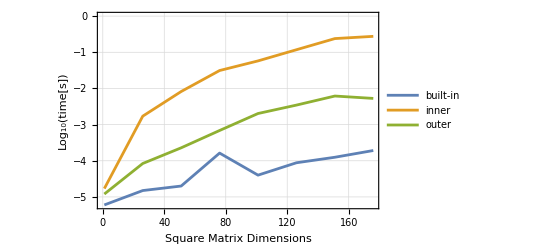

```mathematica
ListLinePlot[{plottableTimings[2],
plottableTimings[3],plottableTimings[4]},
(*ImageSize->Large,*)GridLines->Automatic,
Frame->True,PlotLegends->{"built-in","inner","outer"},
FrameLabel->{{"Log_10(time[s])",""},{"Square Matrix Dimensions","Running Times"}}]
```

## Table 1 — VSR and ACC

Kuzma presents a worked-out example for his IBM POWER10 MMA chip, which has VSRs of 128 bits and ACCs of 512 bits. The bits in these registers can handle seven different types of elements. The computation size in the table implies tile sizes m×k and k×n that produce results that fit in an ACC of 512 bits. The first worked example below approximates this with tiles of small size that can be visually checked in the paper. Tiles in the APU are much larger, 1×2048 for example and more difficult to visualize. Therefore, we present examples with large APU tiles after we have vetted the algorithm.

```mathematica
ClearAll[mmaI,mmaI4,mmaI8,mmaI16,mmaBf16,mmaF16,mmaF32,mmaF64];
```

The integer MMA instructions for the POWER10 consume four 128-bit VSRs — an ACC, for a total of 512 bits. Up to 32 VSRs can be used, 4 at a time, in this way.

```mathematica
mmaI[bitCount_?(MemberQ[{4,8,16},#]&)]:=
With[{m=4,k=32/bitCount,n=4},
With[{A=RandomInteger[{0,2^bitCount-1},{m,k}],
B=RandomInteger[{0,2^bitCount-1},{k,n}]},
accumulatedOuterProduct[m,k,n,A,B]]]
```

```mathematica
mmaI[8]
```

<|m→4,k→4,n→4,result→{{84507,93728,119382,68767},{89639,50103,76004,40948},{30513,24965,37899,25822},{47083,54222,70036,41510}},time→0.000026 s|>

accumulatedOuterProduct also works as a rank-1 outer product.

```mathematica
accumulatedOuterProduct[5,1,4,({{1}, {2}, {3}, {4}, {5}}),({{7, 11, 13, 19}})]["result"]//MatrixForm
```

(7 | 11 | 13 | 19
14 | 22 | 26 | 38
21 | 33 | 39 | 57
28 | 44 | 52 | 76
35 | 55 | 65 | 95)

## Codegen for GEMM

GEMM is a standard operation in LAPACK.

### Algorithm 1

A, B, APack, BPack, AccTile, ATile, BTile, ABTile, CTile, and CNewTile are free-variable pointers to memory. nr , kr, mr are free packing parameters. In my opinion, they would be better called tiling parameters because they’re tuned to the intrinsic LLVM on line 12, but I’ll follow the paper’s nomenclature for now. nc, kc, mc are free blocking parameters that divide matrices into blocks appropriately sized and ordered (row-major versus column-order) for cache. lda, ldb, ldc are free leading dimensions, thus strides, and pertain to either row-major or column-major storage conventions. The pack function reorders blocks into row-major or column-major order as needed for optimal tile-multiplication speed. α and β are free scalar parameters required by GEMM. My implementation refactors Algorithm 1 for greater clarity. Later, we show a direct transcription of Algorithm 1 and compare it to our refactored form.

```mathematica
ClearAll[packingParameters,mr,kr,nr,blockingParameters,mc,kc,nc,A,APack,B,BPack,leadingDimensions,lda,ldb,ldc,ATile,BTile,AccTile,ABTile,CTile,CNewTile,β,α];
packingParameters={mr,kr,nr};
blockingParameters={mc,kc,nc};
leadingDimensions={lda,ldb,ldc};
```

M, K, N are original dimensions: M×K for AOriginal, K×N for BOriginal. kc (block size) must divide K; mc (block size) must divide M, nc (block size) must divide N. If not, the original matrices, AOriginal and BOriginal, must be padded out with zeros to integer multiples of mc, kc, nc. Such is preprocessing, not described here. Likewise, mr (tile size) must divide mc, kr (tile size) must divide kc, and nr (tile size) must divide nc.

In the following illustration, AOriginal and BOriginal are stored in column-major order.

Let us mechanize a concrete version of this illustration by ignoring most ellipses (triple dots). An exception is the picture of B, for which we increase kc from 2kr to 3kr for consistency with the picture of A. The two pictures for A and for B represent the (4,2) and (2,2) 1-indexed blocks, respectively, of the original matrices, AOriginal and BOriginal.

## Compiling MatMul to Blocks and Tiles

### tileMul

Everything gets compiled to calls of tileMul. This is our refactored stand-in for the loop over llvm.matrix.multiply on lines 9 through 13 of Algorithm 1. Our stand-in for llvm.matrix.multiply itself is an invocation of Mathematica’s built-in Dot operator.

tileMul multiplies blocks that contain small tiles, multiplying each tile at maximum speed in the machine. A tile is a sub-matrix that snugly fits in the particular machine registers used for multiplication. tileMul is here parameterized to the dimensions of blocks and tiles so that we can compile to various devices, such as the Gemini-I APU and the Gemini-II APU, which differ in dimensions.

tileMul takes a pair of blocks with snug tiles inside, then triples of integers for inner and outer dimensions. The three outer dimensions, mc, kc, and nc, are dimensions of block multiplicands, mc×kc and kc×nc. The three inner dimensions, mr, kr, and nr, are dimensions of tile multiplicands, mr×kr and kr×nr. Each inner dimension must evenly divide the corresponding outer dimension, meaning that tiles must partition blocks, that is, fit in blocks with no gaps or overlaps. The number of block rows must be an integer multiple of the number of tile rows, and likewise for columns. Each of mc/mr, kc/kr, and nc/nr must be integers.

As an illustration, consider the following two tiled blocks.

```mathematica
aBlockTiled$=({{({{15, 14, 10, 15}, {3, 9, 8, 5}}), ({{6, 0, 3, 8}, {5, 10, 9, 6}}), ({{3, 14, 1, 1}, {6, 1, 14, 4}})}, {({{11, 14, 9, 10}, {11, 13, 3, 3}}), ({{12, 2, 0, 15}, {5, 3, 15, 13}}), ({{5, 4, 14, 1}, {13, 4, 7, 3}})}, {({{12, 7, 14, 14}, {15, 6, 14, 13}}), ({{2, 7, 15, 15}, {1, 13, 0, 8}}), ({{5, 0, 9, 1}, {14, 5, 2, 10}})}});
bBlockTiled$=({{({{9, 4}, {4, 1}, {11, 9}, {15, 3}}), ({{9, 13}, {14, 12}, {9, 13}, {12, 13}}), ({{6, 7}, {7, 11}, {10, 3}, {7, 15}}), ({{12, 3}, {8, 4}, {0, 13}, {3, 12}}), ({{4, 11}, {8, 11}, {5, 4}, {5, 5}})}, {({{13, 15}, {14, 2}, {0, 13}, {10, 0}}), ({{7, 0}, {10, 15}, {3, 15}, {8, 7}}), ({{1, 4}, {6, 6}, {15, 6}, {11, 7}}), ({{15, 5}, {11, 6}, {15, 6}, {11, 11}}), ({{5, 8}, {14, 10}, {8, 15}, {5, 15}})}, {({{3, 14}, {10, 10}, {7, 5}, {10, 8}}), ({{0, 3}, {14, 5}, {6, 1}, {0, 3}}), ({{5, 3}, {9, 7}, {13, 2}, {14, 12}}), ({{5, 2}, {11, 15}, {1, 10}, {7, 5}}), ({{9, 12}, {11, 0}, {2, 7}, {8, 6}})}});
```

The outer dimensions of the pair (aBlockTiled$, bBlockTiled$) are mc=(3×(mr=2))=6 (three rows of 2-row tiles in aBlockTiled$), kc=(3×(kr=4))=12 (three columns of 4-column tiles in aBlockTiled$, and three rows of 4-row tiles in bBlockTiled$), and nc=(5×(nr=2))=10 (five columns of 2-column tiles in bBlockTiled$). The inner dimensions are mr=2, kr=4, nr=2, corresponding respectively to the row dimension, mr, of a left-multiplicand tile; to the column dimension, kr, of a left-multiplicand tile, equal to the row dimension of a right-multiplicand tile; and to the column dimension, nr, of a right-multiplicand tile.

Notice that nr must equal mr because tiles are of transposed shapes on the left and the right of our tile product. This restriction does not pertain to Kuzma’s original Algorithm 1, only to our refactoring of it. The API has separate parameters for them for the sake of symmetry in the API, making it easier to remember.

Let’s define tileMul as an iterated inner product of tiles and accumulated outer product within the tiles, then apply it to these examples:

```mathematica
ClearAll[tileMul];
tileMul[ATiles_,BTiles_,mc_,kc_,nc_,mr_,kr_,nr_]:=
Module[{tm,tk,tn,CTile,McByMr=mc/mr,KcByKr=kc/kr,NcByNr=nc/nr},
CTile=ConstantArray[ConstantArray[0,{mr,nr}],{McByMr,NcByNr}];
For[tm=1,tm<=McByMr,tm++,(* for each row of A's tiles *)
For[tn=1,tn<=NcByNr,tn++,(* for each column in B's tiles *)
For[tk=1,tk<=KcByKr,tk++,(* iterated inner products of tiles *)
(* ATiles⟦tm,tk⟧.BTiles⟦tk,tn⟧ implicitly by accumulated outer product *)
CTile[[tm,tn]]+=ATiles[[tm,tk]].BTiles[[tk,tn]]]]];
CTile];
```

```mathematica
tileMul[aBlockTiled$,bBlockTiled$,6,12,10,2,4,2]//MatrixForm
```

((850 | 533
657 | 516) | (918 | 872
593 | 692) | (700 | 733
739 | 496) | (737 | 778
592 | 601) | (582 | 696
541 | 748)
(901 | 541
624 | 650) | (860 | 745
656 | 813) | (770 | 656
833 | 610) | (731 | 778
858 | 607) | (539 | 866
629 | 1004)
(862 | 585
989 | 608) | (803 | 1066
784 | 968) | (949 | 703
811 | 747) | (780 | 826
710 | 751) | (618 | 1000
735 | 852))

To check this result against a straightforward matrix product, we must flatten the tile level.

### untileBlock

Is the result above equivalent to the matrix product aBlockTiled$.bBlockTiled$? First define untileBlock, which does exactly what its name says.

```mathematica
ClearAll[untileBlock];
untileBlock[ATiledBlock_,mr_,mc_,kr_,kc_]:=
(* Produce 1 mc×kc block from its tiles, each mr×kr. *)
Module[{ABlock=ConstantArray[0,{mc,kc}],tileI,tileJ,inI,inJ,bm,bk},
For[bm=1,bm<=mc,bm++,
For[bk=1,bk<=kc,bk++,
tileI=1+Quotient[(bm-1),mr];
tileJ=1+Quotient[(bk-1),kr];
inI=1+Mod[(bm-1),mr];
inJ=1+Mod[(bk-1),kr];
ABlock[[bm,bk]]=ATiledBlock[[tileI,tileJ,inI,inJ]]]];
ABlock];
```

Apply untileBlock to aBlockTiled$ and to bBlockTiled$., compute the matrix product via Wolfram’s built-in, then visually check that the untiled matrices match their tiled brethren above.

```mathematica
(aBlock$=untileBlock[aBlockTiled$,2,6,4,12])//MatrixForm
(bBlock$=untileBlock[bBlockTiled$,4,12,2,10])//MatrixForm
(cBlock$=aBlock$.bBlock$)//MatrixForm
```

(15 | 14 | 10 | 15 | 6 | 0 | 3 | 8 | 3 | 14 | 1 | 1
3 | 9 | 8 | 5 | 5 | 10 | 9 | 6 | 6 | 1 | 14 | 4
11 | 14 | 9 | 10 | 12 | 2 | 0 | 15 | 5 | 4 | 14 | 1
11 | 13 | 3 | 3 | 5 | 3 | 15 | 13 | 13 | 4 | 7 | 3
12 | 7 | 14 | 14 | 2 | 7 | 15 | 15 | 5 | 0 | 9 | 1
15 | 6 | 14 | 13 | 1 | 13 | 0 | 8 | 14 | 5 | 2 | 10)

(9 | 4 | 9 | 13 | 6 | 7 | 12 | 3 | 4 | 11
4 | 1 | 14 | 12 | 7 | 11 | 8 | 4 | 8 | 11
11 | 9 | 9 | 13 | 10 | 3 | 0 | 13 | 5 | 4
15 | 3 | 12 | 13 | 7 | 15 | 3 | 12 | 5 | 5
13 | 15 | 7 | 0 | 1 | 4 | 15 | 5 | 5 | 8
14 | 2 | 10 | 15 | 6 | 6 | 11 | 6 | 14 | 10
0 | 13 | 3 | 15 | 15 | 6 | 15 | 6 | 8 | 15
10 | 0 | 8 | 7 | 11 | 7 | 11 | 11 | 5 | 15
3 | 14 | 0 | 3 | 5 | 3 | 5 | 2 | 9 | 12
10 | 10 | 14 | 5 | 9 | 7 | 11 | 15 | 11 | 0
7 | 5 | 6 | 1 | 13 | 2 | 1 | 10 | 2 | 7
10 | 8 | 0 | 3 | 14 | 12 | 7 | 5 | 8 | 6)

(850 | 533 | 918 | 872 | 700 | 733 | 737 | 778 | 582 | 696
657 | 516 | 593 | 692 | 739 | 496 | 592 | 601 | 541 | 748
901 | 541 | 860 | 745 | 770 | 656 | 731 | 778 | 539 | 866
624 | 650 | 656 | 813 | 833 | 610 | 858 | 607 | 629 | 1004
862 | 585 | 803 | 1066 | 949 | 703 | 780 | 826 | 618 | 1000
989 | 608 | 784 | 968 | 811 | 747 | 710 | 751 | 735 | 852)

### blockIt, tileIt

We now know how to multiply blocks full of snug tiles. We need to partition general matrices into snug blocks, in-turn partitioned into snug tiles. The dimensions of the snug blocks must divide the dimensions of the matrices, but that is the only restriction. If the matrices don’t snugly contain blocks, pad out the matrices in a pre-processing step. We do not consider that padding step in this paper.

Define a pair of functions, blockIt and tileIt, that, respectively, produce a blocked matrix and a tiled block.

```mathematica
ClearAll[blockIt,tileIt];

blockIt[A_,mc_,M_,kc_,K_]:=Table[
A[[m;;m+mc-1,k;;k+kc-1]],{m,1,M,mc},{k,1,K,kc}];

tileIt[ABlock_,mr_,mc_,kr_,kc_]:=Table[
ABlock[[m;;m+mr-1,k;;k+kr-1]],{m,1,mc,mr},{k,1,kc,kr}];
```

Iterate tileIt over the result of blockIt on a matrix to get a doubly partitioned blocked and tiled matrix. Below is an example. Notice we build the dimensions bottom-up to ensure integer divisibility and to avoid padding. The regular structure in the displays is evident and instructive. Strive to see how 2D iterations of tileMul produces desired results.

```mathematica
With[{bitCount=4},
With[{mr=2,kr=4,nr=2},(* -- tiles *)
With[{mc=2mr,kc=2kr,nc=2nr},(* mc=4, kc=8, nc=4 -- blocks *)
With[{M=2mc,K=2kc,N=2nc},(* M=8, K=16, N=8, -- original dims *)
With[{A=RandomInteger[{0,2^bitCount-1},{M,K}],
B=RandomInteger[{0,2^bitCount-1},{K,N}]},
Module[{
ABlocked=blockIt[A,mc,M,kc,K],
BBlocked=blockIt[B,kc,K,nc,N],
ATiled,BTiled},
ATiled=Table[tileIt[ABlocked[[bm,bk]],mr,mc,kr,kc],{bm,1,M/mc},{bk,1,K/kc}];
BTiled=Table[tileIt[BBlocked[[bk,bn]],kr,kc,nr,nc],{bk,1,K/kc},{bn,1,N/nc}];
Column[{(* displays *)
ATiled//MatrixForm,
BTiled//MatrixForm,
<|"dim[A]"->Dimensions[A],
"dim[B]"->Dimensions[B],
"dim[A_blocked]"->Dimensions[ABlocked],
"dim[B_blocked]"->Dimensions[BBlocked],
"A_tiled"->Dimensions[ATiled],
"B_tiled"->Dimensions[BTiled],
"bits"->bitCount,
"mr"->mr,"kr"->kr,"nr"->nr,
"mc"->mc,"kc"->kc,"nc"->nc,
"M"->M,"K"->K,"N"->N|>//Print;}]]]]]]]
```

<|dim[A]→{8,16},dim[B]→{16,8},dim[A_blocked]→{2,2,4,8},dim[B_blocked]→{2,2,8,4},A_tiled→{2,2,2,2,2,4},B_tiled→{2,2,2,2,4,2},bits→4,mr→2,kr→4,nr→2,mc→4,kc→8,nc→4,M→8,K→16,N→8|>

(((11 | 12 | 12 | 6
4 | 3 | 13 | 5) | (5 | 4 | 9 | 1
13 | 6 | 0 | 6)
(12 | 14 | 11 | 13
13 | 0 | 6 | 1) | (15 | 15 | 1 | 6
12 | 9 | 13 | 6)) | ((3 | 3 | 9 | 8
5 | 2 | 11 | 7) | (0 | 13 | 8 | 7
12 | 6 | 14 | 6)
(14 | 7 | 10 | 10
11 | 10 | 15 | 3) | (2 | 4 | 7 | 2
3 | 8 | 0 | 7))
((0 | 14 | 10 | 8
4 | 15 | 5 | 12) | (10 | 9 | 15 | 10
1 | 2 | 7 | 14)
(6 | 4 | 10 | 2
12 | 12 | 14 | 7) | (11 | 11 | 7 | 12
8 | 14 | 1 | 12)) | ((9 | 7 | 4 | 8
2 | 14 | 9 | 15) | (5 | 7 | 6 | 12
4 | 5 | 13 | 1)
(5 | 2 | 8 | 5
11 | 4 | 13 | 0) | (11 | 15 | 1 | 6
15 | 9 | 9 | 7)))
(((14 | 11
7 | 10
9 | 3
2 | 1) | (5 | 15
15 | 0
7 | 5
14 | 4)
(9 | 6
6 | 1
3 | 6
11 | 6) | (10 | 5
1 | 9
13 | 6
4 | 3)) | ((8 | 14
6 | 3
1 | 8
1 | 12) | (6 | 3
14 | 0
10 | 12
0 | 7)
(9 | 4
4 | 11
13 | 12
5 | 8) | (7 | 3
10 | 0
10 | 9
9 | 2))
((14 | 13
7 | 10
8 | 8
7 | 4) | (12 | 2
6 | 13
7 | 12
11 | 5)
(11 | 4
5 | 12
3 | 12
5 | 11) | (2 | 3
15 | 1
13 | 11
1 | 13)) | ((8 | 12
3 | 12
5 | 0
1 | 14) | (1 | 1
6 | 6
13 | 15
12 | 9)
(11 | 11
11 | 9
12 | 1
13 | 0) | (11 | 1
13 | 10
10 | 11
10 | 13)))

### unBlock

unBlock is exactly parallel to untileBlock. It does not need a unit test or an illustrative example.

```mathematica
ClearAll[unblock];

unblock[ABlocked_,mc_,M_,kc_,K_]:=
Module[{A=ConstantArray[0,{M,K}],blockI,blockJ,inI,inJ,m,k},
For[m=1,m<=M,m++,
For[k=1,k<=K,k++,
blockI=1+Quotient[(m-1),mc];
blockJ=1+Quotient[(k-1),kc];
inI=1+Mod[(m-1),mc];
inJ=1+Mod[(k-1),kc];
A[[m,k]]=ABlocked[[blockI,blockJ,inI,inJ]]]];
A];
```

### blockTileMul, blockMul

blockTileMul is the intermediate target of compilation, after matrices have been blocked and tiled as described above. blockTileMul calls tileMul at bottom.

For testing, we include a blockMul routine for blocked-but-not-tiled matrices: the untiled results of blockTileMul must match the results of blockMul, and the unblocked results must match the results of Mathematica’s built-in matrix multiplication. The following defines blockTileMul and blockMul, then Asserts the requirements on an example.

```mathematica
On[Assert];
ClearAll[blockMul,blockTileMul];

blockTileMul[ABlocks_,BBlocks_,M_,K_,N_,mc_,kc_,nc_,mr_,kr_,nr_]:=
(* ABlocks is an array of mc×kc blocks, BBlock of kc×nc blocks. *)
Module[{bm,bk,bn,MByMc=M/mc,KByKc=K/kc,NByNc=N/nc,McByMr=mc/nr,NcByNr=nc/nr,
CTiled,ATiles,BTiles},
CTiled=ConstantArray[ConstantArray[ConstantArray[0,{mr,nr}],
{McByMr,NcByNr}],{MByMc,NByNc}];
(* for each input block *)
For[bm=1,bm<=MByMc,bm++,
For[bn=1,bn<=NByNc,bn++,
(* iterated inner product *)
For[bk=1,bk<=KByKc,bk++,
ATiles=tileIt[ABlocks[[bm,bk]],mr,mc,kr,kc];
BTiles=tileIt[BBlocks[[bk,bn]],kr,kc,nr,nc];
CTiled[[bm,bn]]+=tileMul[ATiles,BTiles,mc,kc,nc,mr,kr,nr]]]];
CTiled];

blockMul[ABlocks_,BBlocks_,M_,K_,N_,mc_,kc_,nc_,mr_,kr_,nr_]:=
Module[{bm,bk,bn,MByMc=M/mc,KByKc=K/kc,NByNc=N/nc,McByMr=mc/nr,NcByNr=nc/nr,
CBlocked},
CBlocked=ConstantArray[ConstantArray[0,{mc,nc}],{MByMc,NByNc}];
(* for each input block *)
For[bm=1,bm<=MByMc,bm++,
For[bn=1,bn<=NByNc,bn++,
(* iterated inner product *)
For[bk=1,bk<=KByKc,bk++,
CBlocked[[bm,bn]]+=ABlocks[[bm,bk]].BBlocks[[bk,bn]]]]];
CBlocked];

With[{bitCount=4},
With[{mr=2,kr=4,nr=2},(* -- tiles *)
With[{mc=3mr,kc=3kr,nc=5nr},(* mc=6, kc=12, nc=10 -- blocks *)
With[{M=5mc,K=3kc,N=3nc},(* M=30, K=36, N=30, -- original dims *)
With[{A=RandomInteger[{0,2^bitCount-1},{M,K}],
B=RandomInteger[{0,2^bitCount-1},{K,N}]},
Module[{
ABlocks=blockIt[A,mc,M,kc,K],
BBlocks=blockIt[B,kc,K,nc,N],
CTiled,CBlocked,CBlockedCheck,C,CCheck,bm,bk,bn,tm,tk,tn},
CTiled=blockTileMul[ABlocks,BBlocks,M,K,N,mc,kc,nc,mr,kr,nr];
(* Check intermediate forms. *)
CBlocked=Table[untileBlock[CTiled[[m,n]],mr,mc,nr,nc],{m,1,M/mc},{n,1,N/nc}];
CBlockedCheck=blockMul[ABlocks,BBlocks,M,K,N,mc,kc,nc,mr,kr,nr];
Assert[CBlockedCheck===CBlocked];
C=unblock[CBlocked,mc,M,nc,N];
CCheck=A.B;
Assert[CCheck===C];
Column[{(* displays *)
A//MatrixForm;
B//MatrixForm;
ABlocks//MatrixForm;
BBlocks//MatrixForm;
CTiled//MatrixForm,
CBlockedCheck//MatrixForm;
CBlocked//MatrixForm;
C//MatrixForm,
<|"dim[A]"->Dimensions[A],
"dim[B]"->Dimensions[B],
"dim[C_tiled]"->Dimensions[CTiled],
"dim[A_blocks]"->Dimensions[ABlocks],
"dim[B_blocks]"->Dimensions[BBlocks],
"dim[C]"->Dimensions[C],
"bits"->bitCount,
"mr"->mr,"kr"->kr,"nr"->nr,
"mc"->mc,"kc"->kc,"nc"->nc,
"M"->M,"K"->K,"N"->N|>//Print;}]]]]]]]
```

<|dim[A]→{30,36},dim[B]→{36,30},dim[C_tiled]→{5,3,3,5,2,2},dim[A_blocks]→{5,3,6,12},dim[B_blocks]→{3,3,12,10},dim[C]→{30,30},bits→4,mr→2,kr→4,nr→2,mc→6,kc→12,nc→10,M→30,K→36,N→30|>

(((1848 | 1547
2100 | 1772) | (1957 | 1851
2190 | 2235) | (1580 | 2145
1808 | 2719) | (2058 | 1863
2061 | 2485) | (2227 | 2123
2402 | 2101)
(2218 | 1919
1484 | 1339) | (2522 | 2276
1774 | 1918) | (2270 | 2739
1493 | 2082) | (2415 | 2400
1597 | 1851) | (2715 | 2614
1984 | 2134)
(2092 | 1572
1884 | 1726) | (2193 | 1791
2171 | 2137) | (1663 | 2350
1844 | 2485) | (2096 | 1970
1856 | 2429) | (2210 | 2320
2416 | 2053)) | ((1618 | 1581
1891 | 1958) | (1933 | 1291
2016 | 1654) | (1742 | 1682
1827 | 2077) | (1772 | 1769
1753 | 2224) | (1790 | 2230
2001 | 2330)
(2242 | 2339
1441 | 1789) | (2453 | 1865
1708 | 1534) | (1975 | 2136
1658 | 1748) | (2095 | 2569
1455 | 1906) | (2285 | 2360
1725 | 1879)
(1721 | 2069
1802 | 2071) | (1929 | 1629
2051 | 1831) | (1793 | 2101
1890 | 1996) | (1593 | 2093
1701 | 2101) | (2013 | 2231
2167 | 2107)) | ((1667 | 1897
2098 | 2099) | (1905 | 1627
2117 | 2130) | (1969 | 2130
1966 | 2355) | (1782 | 1645
1812 | 2022) | (1999 | 1623
2020 | 1587)
(2238 | 2377
1761 | 1777) | (2471 | 2242
1955 | 1928) | (2637 | 2593
2085 | 1867) | (2084 | 2196
1869 | 1958) | (2193 | 2081
1612 | 1355)
(1933 | 2041
2119 | 2193) | (1771 | 1739
2318 | 2185) | (2077 | 2131
2416 | 2257) | (1968 | 1940
2140 | 2213) | (1662 | 1638
2171 | 1891))
((2016 | 1413
2248 | 2019) | (2038 | 2070
2455 | 2396) | (1818 | 2603
1849 | 2810) | (1592 | 2237
2422 | 2490) | (2345 | 2140
2494 | 2132)
(2429 | 2055
1884 | 1665) | (2808 | 2528
2035 | 2173) | (2135 | 2908
1773 | 2280) | (2250 | 2698
2234 | 2096) | (2716 | 2465
2480 | 2249)
(1708 | 1326
2290 | 1748) | (1954 | 1883
2361 | 2204) | (1594 | 2200
1753 | 2721) | (1844 | 2073
2105 | 2227) | (2024 | 2043
2183 | 2165)) | ((1948 | 2083
2147 | 2179) | (1843 | 1737
2269 | 1690) | (1948 | 1919
1915 | 2174) | (1718 | 2021
2021 | 2255) | (2017 | 2082
2014 | 2499)
(2318 | 2828
1955 | 2350) | (2322 | 2249
2120 | 1821) | (2050 | 2559
1880 | 1912) | (2166 | 2640
1924 | 2208) | (2394 | 2564
2144 | 2171)
(1534 | 1993
1792 | 2032) | (1758 | 1477
2171 | 1746) | (1826 | 1995
1773 | 2138) | (1657 | 2134
1863 | 2154) | (1952 | 1949
1993 | 2310)) | ((2126 | 2417
2164 | 2576) | (2288 | 2071
2191 | 2033) | (1801 | 2125
2422 | 2419) | (2052 | 2192
2229 | 2120) | (1892 | 1453
2209 | 1895)
(2548 | 2857
2223 | 2115) | (2809 | 2389
2052 | 2072) | (2766 | 2507
2443 | 2304) | (2568 | 2651
2102 | 2288) | (2057 | 2210
2148 | 1879)
(1759 | 2124
2095 | 2493) | (2012 | 1778
1889 | 1804) | (1599 | 1985
2452 | 2310) | (1779 | 1861
2060 | 2045) | (1649 | 1349
1830 | 1951))
((1377 | 1235
2123 | 1663) | (1436 | 1482
2374 | 1804) | (1238 | 1792
1762 | 2598) | (1088 | 1482
2056 | 2298) | (1630 | 1467
2240 | 2102)
(2042 | 1882
2294 | 2177) | (2314 | 2072
2506 | 2272) | (1781 | 2384
2305 | 2591) | (2032 | 2097
2289 | 2136) | (2113 | 2225
2680 | 2360)
(1712 | 1588
1973 | 1534) | (2005 | 1536
2115 | 2108) | (1741 | 1981
1684 | 2449) | (1894 | 2186
1858 | 2220) | (2138 | 1959
2107 | 2324)) | ((1196 | 1272
2018 | 2083) | (1438 | 1213
1853 | 1627) | (1353 | 1302
1881 | 1989) | (1150 | 1263
1613 | 2080) | (1522 | 1538
2263 | 2195)
(2011 | 2107
2219 | 2500) | (2163 | 1747
2473 | 2001) | (1678 | 1940
2038 | 2325) | (1910 | 2145
2061 | 2530) | (1979 | 1914
2501 | 2337)
(1544 | 1956
1594 | 2014) | (1561 | 1206
2232 | 1689) | (1785 | 1797
1816 | 1936) | (1585 | 1883
1891 | 2140) | (1665 | 1714
2016 | 2176)) | ((1392 | 1519
2014 | 2379) | (1433 | 1391
2154 | 1805) | (1374 | 1616
1978 | 2090) | (1538 | 1484
2092 | 2009) | (1403 | 946
1926 | 1775)
(2054 | 2261
2288 | 2405) | (2410 | 1922
2597 | 2225) | (2332 | 2126
2352 | 2550) | (2037 | 2095
2153 | 2222) | (1793 | 1835
2368 | 2201)
(1619 | 1852
2116 | 2125) | (2187 | 1597
2075 | 1751) | (2015 | 1757
2171 | 2266) | (2010 | 2091
1803 | 2060) | (1602 | 1452
2033 | 1572))
((2069 | 1719
1845 | 1844) | (2320 | 2119
2309 | 2128) | (1703 | 2667
1843 | 2801) | (1829 | 2187
2067 | 2504) | (2309 | 2396
2356 | 2157)
(2236 | 1615
2134 | 1667) | (2332 | 2062
2280 | 2167) | (1864 | 2712
1976 | 2343) | (2216 | 2467
2127 | 2216) | (2548 | 2409
2501 | 2160)
(1739 | 1561
2041 | 1956) | (1952 | 1914
2365 | 2423) | (1669 | 2387
2110 | 2550) | (1941 | 2094
2193 | 2390) | (2357 | 1915
2679 | 2537)) | ((1820 | 2147
2026 | 2134) | (2003 | 2036
2250 | 1925) | (1921 | 2233
1931 | 1906) | (1639 | 2187
1819 | 2089) | (2086 | 2411
2072 | 2321)
(1611 | 1821
1891 | 2327) | (2202 | 1704
2102 | 1681) | (1763 | 2167
1754 | 2157) | (1942 | 2327
1855 | 2355) | (1872 | 2423
1921 | 2279)
(1710 | 2093
2120 | 2423) | (1873 | 1723
2206 | 1820) | (1599 | 1992
1963 | 2145) | (1642 | 2016
1833 | 2282) | (1963 | 2024
2222 | 2404)) | ((2032 | 2361
2170 | 2534) | (2279 | 1826
2111 | 2022) | (2170 | 2382
2349 | 2306) | (2121 | 2049
2357 | 2167) | (1928 | 1710
2124 | 1757)
(2171 | 2089
1940 | 2318) | (2402 | 2112
2432 | 2073) | (2599 | 2254
2196 | 2190) | (2017 | 2234
2033 | 1992) | (2012 | 1743
1885 | 1778)
(1766 | 2145
2046 | 2205) | (2134 | 1972
2433 | 2151) | (1936 | 2052
2072 | 2652) | (1911 | 2002
2009 | 2202) | (1707 | 1701
2453 | 1733))
((2130 | 1689
1784 | 1708) | (2338 | 1975
2385 | 1969) | (1868 | 2398
1839 | 2531) | (2139 | 2357
1960 | 2422) | (2598 | 2133
2364 | 1963)
(1930 | 1829
1992 | 1727) | (2191 | 2091
2110 | 1958) | (1599 | 2218
1666 | 2189) | (2276 | 2006
2039 | 1673) | (2238 | 2100
2185 | 2124)
(2340 | 2247
2359 | 1833) | (2625 | 2615
2537 | 2284) | (2164 | 2791
1996 | 2757) | (2701 | 2481
2249 | 2489) | (2978 | 2646
2706 | 2244)) | ((1946 | 2094
1873 | 2330) | (2049 | 1752
1931 | 1735) | (1707 | 1969
1692 | 2068) | (1943 | 2070
1557 | 2141) | (1775 | 2158
1897 | 2234)
(1533 | 2163
1704 | 2024) | (1862 | 1654
1882 | 1640) | (1749 | 1941
1531 | 1965) | (1650 | 2089
1708 | 2202) | (2040 | 2244
1852 | 2206)
(2233 | 2409
2138 | 2079) | (2523 | 2003
2311 | 1802) | (2088 | 2371
1900 | 2104) | (2133 | 2554
2216 | 2194) | (2313 | 2753
1952 | 2601)) | ((2169 | 2170
1782 | 2085) | (2017 | 1890
2044 | 1943) | (2308 | 2174
2348 | 2122) | (2148 | 2154
2039 | 2230) | (1812 | 1719
1904 | 1743)
(1873 | 2244
1878 | 1933) | (2038 | 1489
2211 | 1849) | (2077 | 2001
2050 | 2000) | (2105 | 2139
1920 | 1857) | (1853 | 1802
1735 | 1643)
(2215 | 2198
2193 | 2470) | (2580 | 2307
2332 | 2144) | (2829 | 2777
2615 | 2586) | (2246 | 2422
2198 | 2158) | (2649 | 2239
2155 | 2023)))
(1848 | 1547 | 1957 | 1851 | 1580 | 2145 | 2058 | 1863 | 2227 | 2123 | 1618 | 1581 | 1933 | 1291 | 1742 | 1682 | 1772 | 1769 | 1790 | 2230 | 1667 | 1897 | 1905 | 1627 | 1969 | 2130 | 1782 | 1645 | 1999 | 1623
2100 | 1772 | 2190 | 2235 | 1808 | 2719 | 2061 | 2485 | 2402 | 2101 | 1891 | 1958 | 2016 | 1654 | 1827 | 2077 | 1753 | 2224 | 2001 | 2330 | 2098 | 2099 | 2117 | 2130 | 1966 | 2355 | 1812 | 2022 | 2020 | 1587
2218 | 1919 | 2522 | 2276 | 2270 | 2739 | 2415 | 2400 | 2715 | 2614 | 2242 | 2339 | 2453 | 1865 | 1975 | 2136 | 2095 | 2569 | 2285 | 2360 | 2238 | 2377 | 2471 | 2242 | 2637 | 2593 | 2084 | 2196 | 2193 | 2081
1484 | 1339 | 1774 | 1918 | 1493 | 2082 | 1597 | 1851 | 1984 | 2134 | 1441 | 1789 | 1708 | 1534 | 1658 | 1748 | 1455 | 1906 | 1725 | 1879 | 1761 | 1777 | 1955 | 1928 | 2085 | 1867 | 1869 | 1958 | 1612 | 1355
2092 | 1572 | 2193 | 1791 | 1663 | 2350 | 2096 | 1970 | 2210 | 2320 | 1721 | 2069 | 1929 | 1629 | 1793 | 2101 | 1593 | 2093 | 2013 | 2231 | 1933 | 2041 | 1771 | 1739 | 2077 | 2131 | 1968 | 1940 | 1662 | 1638
1884 | 1726 | 2171 | 2137 | 1844 | 2485 | 1856 | 2429 | 2416 | 2053 | 1802 | 2071 | 2051 | 1831 | 1890 | 1996 | 1701 | 2101 | 2167 | 2107 | 2119 | 2193 | 2318 | 2185 | 2416 | 2257 | 2140 | 2213 | 2171 | 1891
2016 | 1413 | 2038 | 2070 | 1818 | 2603 | 1592 | 2237 | 2345 | 2140 | 1948 | 2083 | 1843 | 1737 | 1948 | 1919 | 1718 | 2021 | 2017 | 2082 | 2126 | 2417 | 2288 | 2071 | 1801 | 2125 | 2052 | 2192 | 1892 | 1453
2248 | 2019 | 2455 | 2396 | 1849 | 2810 | 2422 | 2490 | 2494 | 2132 | 2147 | 2179 | 2269 | 1690 | 1915 | 2174 | 2021 | 2255 | 2014 | 2499 | 2164 | 2576 | 2191 | 2033 | 2422 | 2419 | 2229 | 2120 | 2209 | 1895
2429 | 2055 | 2808 | 2528 | 2135 | 2908 | 2250 | 2698 | 2716 | 2465 | 2318 | 2828 | 2322 | 2249 | 2050 | 2559 | 2166 | 2640 | 2394 | 2564 | 2548 | 2857 | 2809 | 2389 | 2766 | 2507 | 2568 | 2651 | 2057 | 2210
1884 | 1665 | 2035 | 2173 | 1773 | 2280 | 2234 | 2096 | 2480 | 2249 | 1955 | 2350 | 2120 | 1821 | 1880 | 1912 | 1924 | 2208 | 2144 | 2171 | 2223 | 2115 | 2052 | 2072 | 2443 | 2304 | 2102 | 2288 | 2148 | 1879
1708 | 1326 | 1954 | 1883 | 1594 | 2200 | 1844 | 2073 | 2024 | 2043 | 1534 | 1993 | 1758 | 1477 | 1826 | 1995 | 1657 | 2134 | 1952 | 1949 | 1759 | 2124 | 2012 | 1778 | 1599 | 1985 | 1779 | 1861 | 1649 | 1349
2290 | 1748 | 2361 | 2204 | 1753 | 2721 | 2105 | 2227 | 2183 | 2165 | 1792 | 2032 | 2171 | 1746 | 1773 | 2138 | 1863 | 2154 | 1993 | 2310 | 2095 | 2493 | 1889 | 1804 | 2452 | 2310 | 2060 | 2045 | 1830 | 1951
1377 | 1235 | 1436 | 1482 | 1238 | 1792 | 1088 | 1482 | 1630 | 1467 | 1196 | 1272 | 1438 | 1213 | 1353 | 1302 | 1150 | 1263 | 1522 | 1538 | 1392 | 1519 | 1433 | 1391 | 1374 | 1616 | 1538 | 1484 | 1403 | 946
2123 | 1663 | 2374 | 1804 | 1762 | 2598 | 2056 | 2298 | 2240 | 2102 | 2018 | 2083 | 1853 | 1627 | 1881 | 1989 | 1613 | 2080 | 2263 | 2195 | 2014 | 2379 | 2154 | 1805 | 1978 | 2090 | 2092 | 2009 | 1926 | 1775
2042 | 1882 | 2314 | 2072 | 1781 | 2384 | 2032 | 2097 | 2113 | 2225 | 2011 | 2107 | 2163 | 1747 | 1678 | 1940 | 1910 | 2145 | 1979 | 1914 | 2054 | 2261 | 2410 | 1922 | 2332 | 2126 | 2037 | 2095 | 1793 | 1835
2294 | 2177 | 2506 | 2272 | 2305 | 2591 | 2289 | 2136 | 2680 | 2360 | 2219 | 2500 | 2473 | 2001 | 2038 | 2325 | 2061 | 2530 | 2501 | 2337 | 2288 | 2405 | 2597 | 2225 | 2352 | 2550 | 2153 | 2222 | 2368 | 2201
1712 | 1588 | 2005 | 1536 | 1741 | 1981 | 1894 | 2186 | 2138 | 1959 | 1544 | 1956 | 1561 | 1206 | 1785 | 1797 | 1585 | 1883 | 1665 | 1714 | 1619 | 1852 | 2187 | 1597 | 2015 | 1757 | 2010 | 2091 | 1602 | 1452
1973 | 1534 | 2115 | 2108 | 1684 | 2449 | 1858 | 2220 | 2107 | 2324 | 1594 | 2014 | 2232 | 1689 | 1816 | 1936 | 1891 | 2140 | 2016 | 2176 | 2116 | 2125 | 2075 | 1751 | 2171 | 2266 | 1803 | 2060 | 2033 | 1572
2069 | 1719 | 2320 | 2119 | 1703 | 2667 | 1829 | 2187 | 2309 | 2396 | 1820 | 2147 | 2003 | 2036 | 1921 | 2233 | 1639 | 2187 | 2086 | 2411 | 2032 | 2361 | 2279 | 1826 | 2170 | 2382 | 2121 | 2049 | 1928 | 1710
1845 | 1844 | 2309 | 2128 | 1843 | 2801 | 2067 | 2504 | 2356 | 2157 | 2026 | 2134 | 2250 | 1925 | 1931 | 1906 | 1819 | 2089 | 2072 | 2321 | 2170 | 2534 | 2111 | 2022 | 2349 | 2306 | 2357 | 2167 | 2124 | 1757
2236 | 1615 | 2332 | 2062 | 1864 | 2712 | 2216 | 2467 | 2548 | 2409 | 1611 | 1821 | 2202 | 1704 | 1763 | 2167 | 1942 | 2327 | 1872 | 2423 | 2171 | 2089 | 2402 | 2112 | 2599 | 2254 | 2017 | 2234 | 2012 | 1743
2134 | 1667 | 2280 | 2167 | 1976 | 2343 | 2127 | 2216 | 2501 | 2160 | 1891 | 2327 | 2102 | 1681 | 1754 | 2157 | 1855 | 2355 | 1921 | 2279 | 1940 | 2318 | 2432 | 2073 | 2196 | 2190 | 2033 | 1992 | 1885 | 1778
1739 | 1561 | 1952 | 1914 | 1669 | 2387 | 1941 | 2094 | 2357 | 1915 | 1710 | 2093 | 1873 | 1723 | 1599 | 1992 | 1642 | 2016 | 1963 | 2024 | 1766 | 2145 | 2134 | 1972 | 1936 | 2052 | 1911 | 2002 | 1707 | 1701
2041 | 1956 | 2365 | 2423 | 2110 | 2550 | 2193 | 2390 | 2679 | 2537 | 2120 | 2423 | 2206 | 1820 | 1963 | 2145 | 1833 | 2282 | 2222 | 2404 | 2046 | 2205 | 2433 | 2151 | 2072 | 2652 | 2009 | 2202 | 2453 | 1733
2130 | 1689 | 2338 | 1975 | 1868 | 2398 | 2139 | 2357 | 2598 | 2133 | 1946 | 2094 | 2049 | 1752 | 1707 | 1969 | 1943 | 2070 | 1775 | 2158 | 2169 | 2170 | 2017 | 1890 | 2308 | 2174 | 2148 | 2154 | 1812 | 1719
1784 | 1708 | 2385 | 1969 | 1839 | 2531 | 1960 | 2422 | 2364 | 1963 | 1873 | 2330 | 1931 | 1735 | 1692 | 2068 | 1557 | 2141 | 1897 | 2234 | 1782 | 2085 | 2044 | 1943 | 2348 | 2122 | 2039 | 2230 | 1904 | 1743
1930 | 1829 | 2191 | 2091 | 1599 | 2218 | 2276 | 2006 | 2238 | 2100 | 1533 | 2163 | 1862 | 1654 | 1749 | 1941 | 1650 | 2089 | 2040 | 2244 | 1873 | 2244 | 2038 | 1489 | 2077 | 2001 | 2105 | 2139 | 1853 | 1802
1992 | 1727 | 2110 | 1958 | 1666 | 2189 | 2039 | 1673 | 2185 | 2124 | 1704 | 2024 | 1882 | 1640 | 1531 | 1965 | 1708 | 2202 | 1852 | 2206 | 1878 | 1933 | 2211 | 1849 | 2050 | 2000 | 1920 | 1857 | 1735 | 1643
2340 | 2247 | 2625 | 2615 | 2164 | 2791 | 2701 | 2481 | 2978 | 2646 | 2233 | 2409 | 2523 | 2003 | 2088 | 2371 | 2133 | 2554 | 2313 | 2753 | 2215 | 2198 | 2580 | 2307 | 2829 | 2777 | 2246 | 2422 | 2649 | 2239
2359 | 1833 | 2537 | 2284 | 1996 | 2757 | 2249 | 2489 | 2706 | 2244 | 2138 | 2079 | 2311 | 1802 | 1900 | 2104 | 2216 | 2194 | 1952 | 2601 | 2193 | 2470 | 2332 | 2144 | 2615 | 2586 | 2198 | 2158 | 2155 | 2023)

## Fitting the APU

For the Gemini-I APU, a common tile size is 1×2048, a half-bank’s worth of 16-bit data. tileMul can perform 16-bit by 16-bit multiplication from two input half-banks and leave the 32-bit result in another pair of half banks. Other plausible choices for the width of a tile are 32768, corresponding to 16 half banks in a single APUC core, or 128Kib, corresponding to 64 half banks in four cores of an entire APU.

Notice that 16-bit integer matrix multiplication will not overflow 32 bits.

The following example shows multiplication of 16-bit matrices in tiles of dimension 1×2048. The left-hand multiplicand, A, has dimensions 15×18432 and the right-hand multiplicand, B, has dimensions 18432×15. The output is 15×15 by 32 bits and fits at the left of two VRs in main memory, or in subsequent columns (plats) of one VR in main memory.

A is partitioned into blocks of dimension 3×6144, requiring 9 VRs out of 53 available in L1. B is partitioned into blocks of dimension 6144×5, requiring 15 VRs out of 53 available in L1. Blocks of A and B must be moved into VRs in main memory prior to multiplication. blockTileMul is responsible for data movement, for accumulating results in one or two VRs of main memory, and for moving final results back into L1 for later harvesting by the host computer. The prototype blockTileMul in this paper does no data movement, but it does perform blocked and tiled multiplication. The 15×15 display after the example can be visually checked.

```mathematica
With[{bitCount=16},
With[{mr=1,kr=2048,nr=1},(* -- mr must equal nr -- tiles *)
With[{mc=3mr,kc=3kr,nc=5nr},(* mc=3, kc=6144, nc=5 -- blocks *)
With[{M=5mc,K=3kc,N=3nc},(* M=15, K=18432, N=15, -- original dims *)
With[{A=RandomInteger[{0,2^bitCount-1},{M,K}],
B=RandomInteger[{0,2^bitCount-1},{K,N}]},
Module[{
ABlocks=blockIt[A,mc,M,kc,K],
BBlocks=blockIt[B,kc,K,nc,N],
CTiled,CBlocked,CBlockedCheck,C,CCheck,bm,bk,bn,tm,tk,tn},
CTiled=blockTileMul[ABlocks,BBlocks,M,K,N,mc,kc,nc,mr,kr,nr];
(* Check intermediate forms. *)
CBlocked=Table[untileBlock[CTiled[[m,n]],mr,mc,nr,nc],{m,1,M/mc},{n,1,N/nc}];
CBlockedCheck=blockMul[ABlocks,BBlocks,M,K,N,mc,kc,nc,mr,kr,nr];
Assert[CBlockedCheck===CBlocked];
C=unblock[CBlocked,mc,M,nc,N];
CCheck=A.B;
Assert[CCheck===C];
Column[{(* displays *)
CTiled//MatrixForm,
C//MatrixForm,
<|"dim[A]"->Dimensions[A],
"dim[B]"->Dimensions[B],
"dim[C_tiled]"->Dimensions[CTiled],
"dim[A_blocks]"->Dimensions[ABlocks],
"dim[B_blocks]"->Dimensions[BBlocks],
"dim[C]"->Dimensions[C],
"bits"->bitCount,
"mr"->mr,"kr"->kr,"nr"->nr,
"mc"->mc,"kc"->kc,"nc"->nc,
"M"->M,"K"->K,"N"->N|>//Print;}]]]]]]]
```

<|dim[A]→{15,18432},dim[B]→{18432,15},dim[C_tiled]→{5,3,3,5,1,1},dim[A_blocks]→{5,3,3,6144},dim[B_blocks]→{3,3,6144,5},dim[C]→{15,15},bits→16,mr→1,kr→2048,nr→1,mc→3,kc→6144,nc→5,M→15,K→18432,N→15|>

(((19741736955588) | (19882838458153) | (19832043109345) | (19863845120857) | (19743235251746)
(19657477883688) | (19704987895460) | (19756017886495) | (19636219343292) | (19523173707783)
(19827187138994) | (19921716149153) | (19771346555375) | (19707635831047) | (19579953564411)) | ((19740738733753) | (19922087651112) | (20004241619528) | (19757360015606) | (19801984553071)
(19593296557761) | (19704077978236) | (19847607823863) | (19722306919927) | (19658170440622)
(19674930214017) | (19905681359648) | (19924883412022) | (19730088340654) | (19811895890214)) | ((19928527815507) | (19845733891739) | (19888256090675) | (19845041044581) | (19590829153173)
(19705452657933) | (19682217130111) | (19679249213695) | (19699951672677) | (19535240869070)
(19871310930826) | (19888801147104) | (19780296166240) | (19873554296134) | (19625441246828))
((19572525224791) | (19751578434825) | (19717434263876) | (19550980254455) | (19494385916131)
(19745896152868) | (19924743612260) | (19822617123583) | (19717253487795) | (19655181376482)
(19813329133222) | (19871722404229) | (19798606954812) | (19815053598759) | (19611442961482)) | ((19667748561233) | (19811968634966) | (19758747330465) | (19622054677479) | (19716675750450)
(19684300079789) | (19833437738913) | (19926231858565) | (19790157688543) | (19920324636606)
(19703803255847) | (19831596256928) | (20003892089442) | (19732569456687) | (19849068231920)) | ((19692553117167) | (19721448783089) | (19642766639668) | (19667283308001) | (19491573251461)
(19886649611696) | (19922772709771) | (19817002999672) | (19806622218695) | (19555382452326)
(20056624113320) | (19978026048672) | (19918341477425) | (19839989955254) | (19687310762668))
((20061437767900) | (20052816356900) | (20038798624488) | (19960736371411) | (19813805228694)
(19844609716697) | (19840248961814) | (19743622814256) | (19731086383029) | (19598689343777)
(19881047481288) | (19955439675208) | (19963261802137) | (19898552251105) | (19774692297933)) | ((19958435626173) | (20198323151192) | (20189385045265) | (20067985183012) | (19997275461881)
(19684826418517) | (19843409892926) | (19976237744566) | (19694910128306) | (19709871038797)
(19821627083337) | (20000614463228) | (20107622053734) | (19876161515996) | (19871019107238)) | ((20128723696898) | (20038597106099) | (19906885740060) | (19912243701084) | (19951317326262)
(19858296978348) | (19939503468146) | (19738438850088) | (19822492584773) | (19601651182824)
(20027625143290) | (19990352362672) | (19970192321125) | (19944531617988) | (19742265307911))
((19801627877479) | (19894661322345) | (19786700799313) | (19636054257861) | (19670900125323)
(19826070823789) | (19985263303057) | (19791888371911) | (19739970748986) | (19628794702111)
(19781761653504) | (19934269511495) | (19796815517066) | (19742303187408) | (19660099395032)) | ((19693824267943) | (19869743065562) | (19908336574077) | (19787882736270) | (19726382807563)
(19772328352844) | (19851629446769) | (19963555091928) | (19766194422939) | (19760024472108)
(19690316663528) | (19864801798196) | (19938512966082) | (19795505624818) | (19796436263756)) | ((19825770975770) | (19816537404175) | (19786490947776) | (19800907972080) | (19521323979855)
(19875113619258) | (19960169011429) | (19843274498445) | (19752699423973) | (19670374631473)
(19820970833209) | (19838218825614) | (19747642607228) | (19754590111251) | (19633190789470))
((19832603536699) | (19992970499352) | (19962452780033) | (19745219528934) | (19586680911620)
(19736663773435) | (19755234267074) | (19848607121802) | (19604069359649) | (19553680992128)
(19822914049698) | (19859690749387) | (19881792487750) | (19828762310339) | (19731933161435)) | ((19772130721641) | (19982986690456) | (19995523297418) | (19753440091953) | (19777874917140)
(19638896904574) | (19786797804879) | (19866779623774) | (19641643519154) | (19766568347915)
(19732110873848) | (19838766738710) | (20021298989629) | (19925026054001) | (19843081795260)) | ((20000704727852) | (19795164444036) | (19852722701891) | (19777713349534) | (19710770839312)
(19817145596752) | (19743416626300) | (19765983869110) | (19695304311306) | (19607762043110)
(19932651346166) | (19984361480228) | (19877980683640) | (19882006333431) | (19703268731642)))
(19741736955588 | 19882838458153 | 19832043109345 | 19863845120857 | 19743235251746 | 19740738733753 | 19922087651112 | 20004241619528 | 19757360015606 | 19801984553071 | 19928527815507 | 19845733891739 | 19888256090675 | 19845041044581 | 19590829153173
19657477883688 | 19704987895460 | 19756017886495 | 19636219343292 | 19523173707783 | 19593296557761 | 19704077978236 | 19847607823863 | 19722306919927 | 19658170440622 | 19705452657933 | 19682217130111 | 19679249213695 | 19699951672677 | 19535240869070
19827187138994 | 19921716149153 | 19771346555375 | 19707635831047 | 19579953564411 | 19674930214017 | 19905681359648 | 19924883412022 | 19730088340654 | 19811895890214 | 19871310930826 | 19888801147104 | 19780296166240 | 19873554296134 | 19625441246828
19572525224791 | 19751578434825 | 19717434263876 | 19550980254455 | 19494385916131 | 19667748561233 | 19811968634966 | 19758747330465 | 19622054677479 | 19716675750450 | 19692553117167 | 19721448783089 | 19642766639668 | 19667283308001 | 19491573251461
19745896152868 | 19924743612260 | 19822617123583 | 19717253487795 | 19655181376482 | 19684300079789 | 19833437738913 | 19926231858565 | 19790157688543 | 19920324636606 | 19886649611696 | 19922772709771 | 19817002999672 | 19806622218695 | 19555382452326
19813329133222 | 19871722404229 | 19798606954812 | 19815053598759 | 19611442961482 | 19703803255847 | 19831596256928 | 20003892089442 | 19732569456687 | 19849068231920 | 20056624113320 | 19978026048672 | 19918341477425 | 19839989955254 | 19687310762668
20061437767900 | 20052816356900 | 20038798624488 | 19960736371411 | 19813805228694 | 19958435626173 | 20198323151192 | 20189385045265 | 20067985183012 | 19997275461881 | 20128723696898 | 20038597106099 | 19906885740060 | 19912243701084 | 19951317326262
19844609716697 | 19840248961814 | 19743622814256 | 19731086383029 | 19598689343777 | 19684826418517 | 19843409892926 | 19976237744566 | 19694910128306 | 19709871038797 | 19858296978348 | 19939503468146 | 19738438850088 | 19822492584773 | 19601651182824
19881047481288 | 19955439675208 | 19963261802137 | 19898552251105 | 19774692297933 | 19821627083337 | 20000614463228 | 20107622053734 | 19876161515996 | 19871019107238 | 20027625143290 | 19990352362672 | 19970192321125 | 19944531617988 | 19742265307911
19801627877479 | 19894661322345 | 19786700799313 | 19636054257861 | 19670900125323 | 19693824267943 | 19869743065562 | 19908336574077 | 19787882736270 | 19726382807563 | 19825770975770 | 19816537404175 | 19786490947776 | 19800907972080 | 19521323979855
19826070823789 | 19985263303057 | 19791888371911 | 19739970748986 | 19628794702111 | 19772328352844 | 19851629446769 | 19963555091928 | 19766194422939 | 19760024472108 | 19875113619258 | 19960169011429 | 19843274498445 | 19752699423973 | 19670374631473
19781761653504 | 19934269511495 | 19796815517066 | 19742303187408 | 19660099395032 | 19690316663528 | 19864801798196 | 19938512966082 | 19795505624818 | 19796436263756 | 19820970833209 | 19838218825614 | 19747642607228 | 19754590111251 | 19633190789470
19832603536699 | 19992970499352 | 19962452780033 | 19745219528934 | 19586680911620 | 19772130721641 | 19982986690456 | 19995523297418 | 19753440091953 | 19777874917140 | 20000704727852 | 19795164444036 | 19852722701891 | 19777713349534 | 19710770839312
19736663773435 | 19755234267074 | 19848607121802 | 19604069359649 | 19553680992128 | 19638896904574 | 19786797804879 | 19866779623774 | 19641643519154 | 19766568347915 | 19817145596752 | 19743416626300 | 19765983869110 | 19695304311306 | 19607762043110
19822914049698 | 19859690749387 | 19881792487750 | 19828762310339 | 19731933161435 | 19732110873848 | 19838766738710 | 20021298989629 | 19925026054001 | 19843081795260 | 19932651346166 | 19984361480228 | 19877980683640 | 19882006333431 | 19703268731642)

## Direct Implementation of Algorithm 1

Our refactoring above is arguably easier to understand than the monolithic code of Algorithm 1. We now show, in steps, that they are equivalent. Along the way, we produce a new refactoring, closer to Algorithm 1, which includes correct-by-construction packing and tiling ratios.

### Definitions

A block is a unit of storage optimized for caching. A tile is a unit of storage optimized for matrix multiplication. mc is the number of rows in a block. kc is the number of columns in a block. mr is the number of rows in a tile. kr is the number of columns in a tile. mr must divide mc, and kr must divide kc. Finally, M and K are the dimensions of a matrix that contains one or more blocks. mc must divide M and kr must divide K.

### Indices

Mathematica indices are 1-based. We compute indices 0-based, then index arrays 1-based by incrementing 0-based indices in situ, that is, by adding 1 inside Mathematica’s Part expressions — doubled square brackets. All indices outside Part notations are 0-based.

## Matrix Metadata

A major activity of software engineering is representing data economically, minimizing duplication and satisfying constraints by construction.

For block and tile operations, matrix metadata are (1) block and tile dimensions and (2) identifiers (names and UUIDs). Ratios represent block and matrix dimensions so that they automatically satisfy partitioning constraints (no overlapping, overhangs, or under-hangs).

UUIDs should be managed in a global registry. Here,  to reduce the complexity of this specification, we do not manage UUIDs. User code is responsible for avoiding duplication of UUIDs.

In most programming languages, we’d represent annotated matrices as structs or classes. Mathematica does not have structs or classes, but has several equivalent mechanisms. We’ll employ the most elementary mechanism, Associations, similar to dictionaries in Python or hashmaps in Clojure.

### Helper Function

Check that some datum is a UUID, for satisfying constraints.

```mathematica
ClearAll[uuidQ];
uuidQ[candidate_]:=
Module[{chars=Characters[candidate]},
(chars[[9]]==="-"===chars[[14]]===chars[[19]]===chars[[24]])&&
Module[{hexes=Select[chars,
ToCharacterCode["0"][[1]]<=ToCharacterCode[#][[1]]<=ToCharacterCode["9"][[1]]||
ToCharacterCode["a"][[1]]<=ToCharacterCode[#][[1]]<=ToCharacterCode["f"][[1]]&]},
Length[hexes]===32&&StringQ[candidate]]]
uuidQ[CreateUUID[]]
```

True

### Factory Functions

A blockTileMatrix is a 2D array with suitable metadata. A packedMatrix is a 1D array with suitable metadata.

#### Running Example

Here is an example taken from the Kuzma paper. It has 12 2×4 column-major tiles stored row-major in the block.

```mathematica
(utA$=({{0, 2, 4, 6, 8, 10, 12, 14, a, c, e, g}, {1, 3, 5, 7, 9, 11, 13, 15, b, d, f, h}, {i, k, m, o, q, s, u, w, α, γ, ϵ, η}, {j, l, n, p, r, t, v, x, β, δ, ζ, θ}, {ι, λ, ν, ο, ρ, τ, ϕ, ψ, Δ, Λ, Π, Φ}, {κ, μ, ξ, π, σ, υ, ξ, ω, Θ, Ξ, Σ, Ω}}))//MatrixForm
```

(0 | 2 | 4 | 6 | 8 | 10 | 12 | 14 | a | c | e | g
1 | 3 | 5 | 7 | 9 | 11 | 13 | 15 | b | d | f | h
i | k | m | o | q | s | u | w | α | γ | ϵ | η
j | l | n | p | r | t | v | x | β | δ | ζ | θ
ι | λ | ν | ο | ρ | τ | ϕ | ψ | Δ | Λ | Π | Φ
κ | μ | ξ | π | σ | υ | ξ | ω | Θ | Ξ | Σ | Ω)

makeBlockTileMatrix annotates 2D matrix content. The storage order of elements in tiles must be the same for all tiles in the matrix. The storage order of tiles in blocks must be the same for all blocks in the matrix. All arguments are constrained, that is, type-checked.

```mathematica
ClearAll[makeBlockTileMatrix];
makeBlockTileMatrix[
mr_Integer,kr_Integer,
mcByMr_Integer,kcByKr_Integer,(*dimensional ratios*)
MByMc_Integer,KByKc_Integer,(*dimensional ratios*)
ElementInTileStorageOrder_String/;(ElementInTileStorageOrder==="row"||ElementInTileStorageOrder==="column"),
TileInBlockStorageOrder_String/;(TileInBlockStorageOrder==="row"||TileInBlockStorageOrder==="column"),
matrixContent_List,matrixName_String,uuid_/;(uuid===Null||uuidQ[uuid])]:=
<|"mr"->mr,"kr"->kr,
"mc/mr"->mcByMr,"mc"->mr mcByMr,
"kc/kr"->kcByKr,"kc"->kr kcByKr,
"M/mc"->MByMc,"M"->mr mcByMr MByMc,
"K/kc"->KByKc,"K"->kr kcByKr KByKc,
"element-in-tile storage order"->ElementInTileStorageOrder,
"tile-in-block storage order"->TileInBlockStorageOrder,
"content"->matrixContent,"name"->matrixName,
"uuid"->If[uuid===Null,CreateUUID[],uuid],
"type"->"blockTileMatrix"|>;
btm$=makeBlockTileMatrix[
2(*mr*),4(*kr*),3(*mc/mr*),3(*kc/kr*),1(*M/mc*),1(*K/kc*),
"column"(*element-in-tile storage order*),
"row"(*tile-in-block storage order*),
utA$(*content*),
"unit-test matrix"(*name -- could be empty*),
"e5bdae0c-0ba8-4ad7-95ef-d3fa13ad8920"(*UUID -- could be Null*)]
```

<|mr→2,kr→4,mc/mr→3,mc→6,kc/kr→3,kc→12,M/mc→1,M→6,K/kc→1,K→12,element-in-tile storage order→column,tile-in-block storage order→row,content→{{0,2,4,6,8,10,12,14,a,c,e,g},{1,3,5,7,9,11,13,15,b,d,f,h},{i,k,m,o,q,s,u,w,α,γ,ϵ,η},{j,l,n,p,r,t,v,x,β,δ,ζ,θ},{ι,λ,ν,ο,ρ,τ,ϕ,ψ,Δ,Λ,Π,Φ},{κ,μ,ξ,π,σ,υ,ξ,ω,Θ,Ξ,Σ,Ω}},name→unit-test matrix,uuid→e5bdae0c-0ba8-4ad7-95ef-d3fa13ad8920,type→blockTileMatrix|>

makePackedMatrix annotates 1D packed matrix content. The storage-order metadata drives packing and unpacking processes. There are four possibilities: the element-in-tile storage order can be column or row, and, independently, the tile-in-block storage order can be column or row.

```mathematica
ClearAll[makePackedMatrix];
makePackedMatrix[len_Integer/;(len>=0),
ElementInTileStorageOrder_String/;(ElementInTileStorageOrder==="row"||ElementInTileStorageOrder==="column"),
TileInBlockStorageOrder_String/;(TileInBlockStorageOrder==="row"||TileInBlockStorageOrder==="column"),
content_List,name_String,uuid_/;(uuid===Null||uuidQ[uuid])]:=
<|"len"->len,
"element-in-tile storage order"->ElementInTileStorageOrder,
"tile-in-block storage order"->TileInBlockStorageOrder,
"content"->content,"name"->name,
"uuid"->If[uuid===Null,CreateUUID[],uuid],
"type"->"packedMatrix"|>
```

### Type Checkers

```mathematica
ClearAll[blockTileMatrixQ,packedMatrixQ];
blockTileMatrixQ[it_Association]:=it["type"]==="blockTileMatrix";
blockTileMatrixQ[btm$]
packedMatrixQ[it_Association]:=it["type"]==="packedMatrix"
```

True

### packBlock

Packs one block from a block matrix into a 1D array, following the storage orders specified in the source block matrix. The unit test has column order for elements in tiles and row order for tiles in blocks.

```mathematica
ClearAll[packBlock];
packBlock[m_?blockTileMatrixQ,
(*Pick a single block via 0-based block indices from the middle of a blockTileMatrix*)
fromRowBlock_Integer,fromColumnBlock_Integer,
optionalName_String,uuid_/;(uuid===Null||uuidQ[uuid])]:=
With[{mr=m["mr"],kr=m["kr"]},
With[{mc=mr*m["mc/mr"],kc=kr*m["kc/kr"]},
With[{i=fromRowBlock*mc,k=fromColumnBlock*mc,A=m["content"]},
Module[{ii,kk,tk,tm,Ai=0,len=mc kc,APack},
APack=ConstantArray[0,len];
(* tile iteration -- for each tile in the block *)
If[m["tile-in-block storage order"]==="row",
For[ii=i,ii<i+mc,ii+=mr,
For[kk=k,kk<k+kc,kk+=kr,
If[m["element-in-tile storage order"]==="column",
For[tk=kk ,tk<(kk+kr),tk++,
For[tm=ii,tm<(ii+mr),tm++,
APack[[1+Ai]]=A[[1+tm,1+tk]];Ai++]],
If[m["element-in-tile storage order"]==="row",
For[tm=ii,tm<(ii+mr),tm++,
For[tk=kk ,tk<(kk+kr),tk++,
APack[[1+Ai]]=A[[1+tm,1+tk]];Ai++]],
Throw[752]]]]],
If[m["tile-in-block storage order"]==="column",
For[kk=k,kk<k+kc,kk+=kr,
For[ii=i,ii<i+mc,ii+=mr,
If[m["element-in-tile storage order"]==="column",
For[tk=kk ,tk<(kk+kr),tk++,
For[tm=ii,tm<(ii+mr),tm++,
APack[[1+Ai]]=A[[1+tm,1+tk]];Ai++]],
If[m["element-in-tile storage order"]==="row",
For[tm=ii,tm<(ii+mr),tm++,
For[tk=kk ,tk<(kk+kr),tk++,
APack[[1+Ai]]=A[[1+tm,1+tk]];Ai++]],
Throw[752]]]]],
Throw[753]]];
makePackedMatrix[len,
m["element-in-tile storage order"],m["tile-in-block storage order"],
APack(*content*),optionalName,uuid]]]]];
btp$=packBlock[btm$,0,0,"packed btm","d7a1c986-e579-4a01-9713-a1475c791587"]
```

<|len→72,element-in-tile storage order→column,tile-in-block storage order→row,content→{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,α,β,γ,δ,ϵ,ζ,η,θ,ι,κ,λ,μ,ν,ξ,ο,π,ρ,σ,τ,υ,ϕ,ξ,ψ,ω,Δ,Θ,Λ,Ξ,Π,Σ,Φ,Ω},name→packed btm,uuid→d7a1c986-e579-4a01-9713-a1475c791587,type→packedMatrix|>

### unpackBlock

Unpack a 1D packedMatrix array into a given block-location inside a block matrix, mutating that content. The unit test shows round-tripping column order for elements in tiles and row order for tiles in blocks. The visualization also shows blocks divided by solid lines and tiles divided by dashed lines along with a UUID check.

```mathematica
ClearAll[griddit];
griddit[m_List,mr_,kr_,mcByMr_,kcByKr_]:=
With[{mc=mr mcByMr,kc=kr kcByKr},
Module[{kd=ConstantArray[False,kc],md=ConstantArray[False,mc],mm,kk},
kd[[kc]]=True;md[[mc]]=True;
For[mm=mr,mm<mc,mm+=mr,md[[mm]]=Dashed];
For[kk=kr,kk<kc,kk+=kr,kd[[kk]]=Dashed];
Grid[m,Dividers->{{True,kd,True},{True,md,True}}]]];
ClearAll[unpackBlock];
unpackBlock[
dest_Symbol/;blockTileMatrixQ[dest],(*pattern for mutability*)
m_?packedMatrixQ,
toRowBlock_Integer,toColumnBlock_Integer,
optionalName_String,uuid_/;(uuid===Null||uuidQ[uuid])]:=
(On[Assert];
Assert[m["element-in-tile storage order"]===dest["element-in-tile storage order"]];
Assert[m["tile-in-block storage order"]===dest["tile-in-block storage order"]];
With[{mr=dest["mr"],kr=dest["kr"]},
With[{mc=mr dest["mc/mr"],kc=kr dest["kc/kr"]},
With[{i=toRowBlock mc,k=toRowBlock kc,APack=m["content"]},
Module[{ii,kk,tk,tm,Ai=0,len=mc kc,A=dest["content"]},
(* tile iteration -- for each tile in the block *)
If[m["tile-in-block storage order"]==="row",
For[ii=i,ii<i+mc,ii+=mr,
For[kk=k,kk<k+kc,kk+=kr,(* element iteration *)
If[m["element-in-tile storage order"]==="column",
For[tk=kk ,tk<(kk+kr),tk++,
For[tm=ii,tm<(ii+mr),tm++,
A[[1+tm,1+tk]]=APack[[1+Ai]];Ai++]],
If[m["element-in-tile storage order"]==="row",
For[tm=ii,tm<(ii+mr),tm++,(* element iteration *)
For[tk=kk ,tk<(kk+kr),tk++,
A[[1+tm,1+tk]]=APack[[1+Ai]];Ai++]],
Throw[752]]]]],
If[m["tile-in-block storage order"]==="column",
For[kk=k,kk<k+kc,kk+=kr,
For[ii=i,ii<i+mc,ii+=mr,
If[m["element-in-tile storage order"]==="column",
For[tk=kk ,tk<(kk+kr),tk++,(* element iteration *)
For[tm=ii,tm<(ii+mr),tm++,
A[[1+tm,1+tk]]=APack[[1+Ai]];Ai++]],
If[m["element-in-tile storage order"]==="row",
For[tm=ii,tm<(ii+mr),tm++,(* element iteration *)
For[tk=kk ,tk<(kk+kr),tk++,
A[[1+tm,1+tk]]=APack[[1+Ai]];Ai++]],
Throw[752]]]]],
Throw[753]]];
dest["content"]=A;
dest]]]]);
(* unit test *)
With[{mr=2,kr=4,ignored=0,
mcByMr=3,kcByKr=3,
MByMc=5,KByKc=3},
With[{mc=mr mcByMr,kc=kr kcByKr},
With[{M=mc MByMc,K=kc KByKc},
Module[{house=
makeBlockTileMatrix[mr,kr,mcByMr,kcByKr,MByMc,KByKc,
"column"(*element-in-tile storage order*),
"row"(*tile-in-block storage order*),
ConstantArray[0,{M,K}],"house",Null]},
Print[house["uuid"]];
(*Unevaluated is a pattern for mutability in Mathematica*)
left$=Module[{result=unpackBlock[Unevaluated[house],btp$,1,1,"unpacked",house["uuid"]]},
Print[result["uuid"]];result]]];
Print[left$["content"]//griddit[#,mr,kr,mcByMr,kcByKr]&]]];
```

010ccbcc-c5cc-4284-82dd-2c6ad65c69d2

010ccbcc-c5cc-4284-82dd-2c6ad65c69d2

0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 4 | 6 | 8 | 10 | 12 | 14 | a | c | e | g | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15 | b | d | f | h | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | i | k | m | o | q | s | u | w | α | γ | ϵ | η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | j | l | n | p | r | t | v | x | β | δ | ζ | θ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ι | λ | ν | ο | ρ | τ | ϕ | ψ | Δ | Λ | Π | Φ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | κ | μ | ξ | π | σ | υ | ξ | ω | Θ | Ξ | Σ | Ω | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

Create a numerical example for a left operand because the symbolic result of a multiplication, while instructive, is too lengthy for inspection.

```mathematica
With[{bitcount=2},
With[{mr=2,kr=4,ignored=0,
mcByMr=3,kcByKr=3,
MByMc=5,KByKc=3},
With[{mc=mr mcByMr,kc=kr kcByKr},
With[{M=mc MByMc,K=kc KByKc},
left$=makeBlockTileMatrix[mr,kr,mcByMr,kcByKr,MByMc,KByKc,
"column"(*element-in-tile storage order*),
"row"(*tile-in-block storage order*),
RandomInteger[2^bitcount-1,{M,K}],"left$",Null];
Print[left$["uuid"]];
Print[left$["content"]//griddit[#,mr,kr,mcByMr,kcByKr]&]]]]];
```

dc368700-51c2-4e83-aa45-907a369c3ba3

3 | 1 | 2 | 0 | 1 | 2 | 1 | 1 | 2 | 3 | 2 | 0 | 0 | 2 | 3 | 3 | 2 | 1 | 0 | 3 | 3 | 1 | 3 | 3 | 3 | 3 | 0 | 1 | 3 | 3 | 3 | 0 | 3 | 1 | 2 | 3
1 | 3 | 0 | 1 | 3 | 1 | 2 | 0 | 0 | 3 | 2 | 3 | 0 | 0 | 2 | 2 | 0 | 2 | 3 | 3 | 3 | 1 | 0 | 1 | 0 | 0 | 2 | 2 | 0 | 0 | 1 | 1 | 2 | 2 | 0 | 2
1 | 3 | 0 | 2 | 2 | 1 | 3 | 0 | 0 | 1 | 2 | 2 | 0 | 2 | 1 | 2 | 1 | 3 | 3 | 1 | 3 | 2 | 2 | 3 | 1 | 0 | 0 | 0 | 2 | 3 | 0 | 2 | 3 | 3 | 1 | 1
3 | 3 | 0 | 3 | 3 | 3 | 3 | 3 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 3 | 3 | 1 | 3 | 3 | 2 | 0 | 3 | 3 | 2 | 1 | 3 | 2 | 2 | 1 | 1
1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 3 | 0 | 3 | 0 | 1 | 1 | 0 | 3 | 3 | 1 | 2 | 0 | 2 | 2 | 0 | 3 | 0 | 3 | 3 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 3 | 0
2 | 1 | 2 | 0 | 1 | 0 | 2 | 1 | 1 | 0 | 0 | 2 | 2 | 1 | 1 | 3 | 2 | 1 | 3 | 0 | 2 | 3 | 1 | 2 | 3 | 1 | 3 | 2 | 3 | 3 | 3 | 3 | 1 | 2 | 1 | 0
2 | 3 | 1 | 2 | 2 | 1 | 1 | 1 | 3 | 3 | 0 | 2 | 1 | 0 | 1 | 2 | 1 | 3 | 1 | 0 | 0 | 3 | 3 | 0 | 2 | 0 | 3 | 2 | 2 | 3 | 2 | 0 | 0 | 0 | 1 | 3
1 | 1 | 1 | 3 | 2 | 2 | 3 | 3 | 3 | 3 | 1 | 0 | 1 | 0 | 0 | 2 | 2 | 2 | 3 | 2 | 0 | 0 | 1 | 3 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 3 | 0 | 2 | 0 | 1
3 | 3 | 1 | 2 | 3 | 0 | 0 | 2 | 0 | 3 | 3 | 1 | 1 | 3 | 2 | 2 | 2 | 1 | 3 | 2 | 0 | 2 | 0 | 3 | 1 | 2 | 0 | 0 | 1 | 3 | 2 | 0 | 3 | 1 | 2 | 0
1 | 0 | 1 | 1 | 3 | 2 | 0 | 1 | 0 | 3 | 2 | 1 | 3 | 2 | 3 | 0 | 3 | 3 | 2 | 1 | 1 | 0 | 1 | 1 | 1 | 2 | 1 | 2 | 2 | 3 | 0 | 2 | 2 | 0 | 1 | 0
1 | 2 | 0 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 0 | 0 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 3 | 1 | 1 | 1 | 2 | 2 | 2 | 0 | 3 | 0 | 1 | 3 | 3 | 3 | 2 | 0
2 | 2 | 2 | 2 | 0 | 2 | 2 | 1 | 0 | 2 | 1 | 1 | 2 | 1 | 3 | 0 | 3 | 3 | 0 | 1 | 3 | 3 | 0 | 3 | 2 | 2 | 2 | 1 | 0 | 0 | 3 | 2 | 3 | 1 | 0 | 0
3 | 3 | 2 | 1 | 3 | 0 | 0 | 3 | 3 | 2 | 0 | 0 | 2 | 2 | 2 | 3 | 2 | 0 | 1 | 2 | 1 | 3 | 1 | 2 | 3 | 0 | 3 | 0 | 0 | 3 | 2 | 1 | 1 | 0 | 1 | 0
2 | 0 | 3 | 3 | 2 | 3 | 1 | 3 | 1 | 1 | 1 | 2 | 1 | 3 | 2 | 3 | 2 | 2 | 3 | 3 | 1 | 2 | 3 | 1 | 1 | 2 | 2 | 2 | 1 | 2 | 0 | 2 | 2 | 1 | 0 | 0
3 | 0 | 1 | 0 | 0 | 2 | 1 | 3 | 1 | 2 | 1 | 1 | 3 | 0 | 2 | 0 | 2 | 1 | 3 | 2 | 2 | 2 | 1 | 0 | 0 | 1 | 2 | 2 | 0 | 3 | 2 | 2 | 3 | 0 | 1 | 1
0 | 1 | 1 | 2 | 0 | 0 | 3 | 0 | 3 | 1 | 1 | 1 | 3 | 3 | 1 | 1 | 0 | 1 | 1 | 3 | 2 | 2 | 1 | 3 | 3 | 0 | 0 | 0 | 3 | 0 | 3 | 1 | 2 | 3 | 3 | 3
2 | 1 | 3 | 3 | 0 | 0 | 1 | 3 | 3 | 0 | 2 | 3 | 1 | 3 | 2 | 1 | 3 | 2 | 0 | 3 | 3 | 0 | 0 | 2 | 1 | 2 | 0 | 2 | 0 | 2 | 0 | 2 | 2 | 3 | 2 | 3
1 | 3 | 2 | 1 | 1 | 0 | 3 | 0 | 2 | 1 | 3 | 0 | 1 | 1 | 0 | 3 | 1 | 0 | 0 | 0 | 0 | 2 | 1 | 2 | 0 | 0 | 3 | 1 | 1 | 3 | 1 | 3 | 0 | 2 | 0 | 1
1 | 2 | 1 | 0 | 2 | 2 | 2 | 0 | 0 | 0 | 3 | 1 | 0 | 2 | 1 | 3 | 3 | 1 | 2 | 0 | 0 | 3 | 0 | 3 | 3 | 3 | 0 | 1 | 3 | 0 | 2 | 3 | 0 | 2 | 1 | 0
0 | 3 | 2 | 2 | 0 | 0 | 3 | 0 | 3 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 3 | 3 | 3 | 1 | 3 | 0 | 1 | 2 | 1 | 3 | 0 | 0 | 2 | 3 | 1 | 0 | 2 | 0
0 | 2 | 3 | 1 | 2 | 0 | 3 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 2 | 3 | 1 | 2 | 1 | 2 | 0 | 2 | 3 | 1 | 0 | 1 | 3 | 1 | 3 | 3 | 2 | 1
2 | 1 | 1 | 3 | 0 | 1 | 3 | 3 | 1 | 2 | 2 | 1 | 2 | 2 | 3 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 1 | 1 | 3 | 3 | 0 | 3 | 0 | 2 | 2 | 1 | 0 | 0 | 0 | 3
3 | 0 | 3 | 1 | 1 | 1 | 3 | 0 | 3 | 2 | 1 | 2 | 2 | 1 | 3 | 3 | 0 | 0 | 2 | 2 | 0 | 3 | 3 | 3 | 0 | 1 | 2 | 1 | 1 | 2 | 0 | 3 | 0 | 1 | 1 | 2
2 | 0 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 0 | 1 | 0 | 2 | 0 | 3 | 1 | 2 | 0 | 2 | 2 | 1 | 3 | 2 | 2 | 1 | 3 | 2 | 0 | 1 | 0 | 3 | 2 | 0 | 2
0 | 3 | 2 | 3 | 1 | 2 | 0 | 2 | 2 | 3 | 1 | 3 | 3 | 1 | 3 | 0 | 2 | 1 | 1 | 1 | 0 | 0 | 3 | 2 | 0 | 0 | 3 | 3 | 0 | 0 | 1 | 1 | 0 | 0 | 3 | 1
1 | 0 | 3 | 0 | 1 | 0 | 1 | 2 | 3 | 0 | 3 | 3 | 1 | 3 | 1 | 1 | 3 | 3 | 3 | 2 | 1 | 0 | 2 | 0 | 0 | 2 | 3 | 1 | 2 | 0 | 2 | 3 | 1 | 3 | 1 | 0
1 | 0 | 1 | 2 | 1 | 3 | 1 | 0 | 1 | 1 | 0 | 2 | 2 | 3 | 0 | 0 | 3 | 1 | 2 | 0 | 1 | 3 | 3 | 0 | 1 | 0 | 1 | 2 | 0 | 1 | 3 | 3 | 3 | 3 | 3 | 3
2 | 2 | 0 | 1 | 3 | 0 | 3 | 2 | 2 | 2 | 0 | 0 | 3 | 0 | 2 | 1 | 2 | 0 | 1 | 3 | 0 | 2 | 0 | 3 | 3 | 1 | 0 | 0 | 2 | 1 | 3 | 0 | 2 | 0 | 3 | 2
0 | 2 | 3 | 0 | 3 | 0 | 3 | 0 | 3 | 0 | 0 | 0 | 3 | 1 | 1 | 2 | 2 | 1 | 3 | 0 | 0 | 1 | 2 | 1 | 3 | 0 | 1 | 0 | 2 | 1 | 3 | 0 | 3 | 1 | 1 | 0
0 | 2 | 3 | 1 | 1 | 3 | 3 | 2 | 1 | 2 | 3 | 1 | 2 | 3 | 0 | 0 | 2 | 0 | 3 | 3 | 3 | 1 | 0 | 2 | 2 | 1 | 3 | 2 | 0 | 1 | 2 | 3 | 2 | 1 | 3 | 3

Give an example of a right-hand multiplicand, again reproduced from Kuzma’s Figure 2.

```mathematica
With[{bitcount=2},
With[{kr=4,nr=2,ignored=0,
kcByKr=3,ncByNr=5,
KByKc=3,NByNc=3},
With[{kc=kr kcByKr,nc=nr ncByNr},
With[{K=kc KByKc,N=nc NByNc},
right$=
makeBlockTileMatrix[kr,nr,kcByKr,ncByNr,KByKc,NByNc,
"row"(*element-in-tile storage order*),
"row"(*tile-in-block storage order*),
RandomInteger[2^bitcount-1,{K,N}],"right$",Null];
Print[right$["uuid"]];
Print[right$["content"]//griddit[#,kr,nr,kcByKr,ncByNr]&]]]]]
```

751e28bc-b922-403a-a62b-cfccb5fae96e

0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 3 | 0 | 0 | 1 | 3 | 1 | 1 | 1 | 1 | 3 | 2 | 0 | 0 | 3 | 0 | 2 | 1 | 1 | 0 | 3 | 3 | 3
1 | 3 | 0 | 0 | 3 | 2 | 3 | 2 | 1 | 3 | 1 | 1 | 1 | 0 | 2 | 2 | 0 | 1 | 3 | 2 | 3 | 1 | 2 | 0 | 0 | 1 | 2 | 3 | 2 | 2
3 | 3 | 0 | 3 | 2 | 2 | 0 | 3 | 3 | 0 | 1 | 0 | 1 | 0 | 3 | 0 | 3 | 2 | 2 | 0 | 3 | 0 | 3 | 3 | 1 | 3 | 2 | 2 | 0 | 3
1 | 2 | 1 | 2 | 3 | 3 | 2 | 0 | 2 | 1 | 0 | 3 | 1 | 1 | 2 | 0 | 0 | 1 | 2 | 1 | 3 | 1 | 0 | 2 | 2 | 0 | 1 | 2 | 2 | 3
1 | 2 | 0 | 3 | 1 | 0 | 3 | 2 | 1 | 2 | 3 | 0 | 0 | 1 | 2 | 2 | 0 | 1 | 0 | 2 | 3 | 2 | 3 | 3 | 2 | 3 | 1 | 1 | 0 | 2
2 | 0 | 2 | 2 | 3 | 0 | 3 | 2 | 2 | 0 | 1 | 1 | 2 | 0 | 0 | 1 | 1 | 3 | 1 | 3 | 2 | 0 | 2 | 1 | 2 | 2 | 1 | 0 | 0 | 2
2 | 2 | 1 | 1 | 1 | 2 | 3 | 2 | 1 | 3 | 1 | 1 | 1 | 1 | 0 | 1 | 2 | 0 | 3 | 1 | 0 | 0 | 0 | 2 | 2 | 2 | 3 | 0 | 2 | 2
2 | 0 | 2 | 3 | 3 | 1 | 3 | 0 | 0 | 2 | 0 | 3 | 1 | 3 | 2 | 1 | 3 | 0 | 0 | 1 | 1 | 1 | 2 | 3 | 1 | 3 | 2 | 2 | 2 | 2
2 | 3 | 1 | 2 | 2 | 0 | 3 | 2 | 0 | 1 | 3 | 2 | 0 | 2 | 0 | 0 | 3 | 3 | 0 | 2 | 0 | 3 | 0 | 1 | 2 | 3 | 1 | 0 | 3 | 2
1 | 0 | 1 | 2 | 1 | 3 | 1 | 3 | 3 | 3 | 2 | 3 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 3 | 0 | 1 | 2 | 0 | 0 | 3 | 1 | 2 | 0
2 | 0 | 1 | 1 | 1 | 3 | 0 | 3 | 3 | 2 | 0 | 3 | 1 | 3 | 2 | 0 | 1 | 3 | 2 | 3 | 3 | 2 | 0 | 1 | 1 | 1 | 2 | 3 | 3 | 2
2 | 1 | 1 | 1 | 3 | 0 | 3 | 0 | 3 | 2 | 2 | 3 | 2 | 0 | 3 | 0 | 2 | 0 | 3 | 3 | 3 | 3 | 1 | 2 | 2 | 1 | 1 | 3 | 3 | 2
3 | 3 | 0 | 0 | 1 | 0 | 2 | 2 | 1 | 0 | 1 | 0 | 0 | 2 | 2 | 0 | 0 | 2 | 1 | 1 | 2 | 3 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1
3 | 3 | 2 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 3 | 1 | 3 | 1 | 2 | 1 | 2 | 2 | 3 | 0 | 0 | 1 | 3 | 1 | 2 | 3 | 3 | 0 | 2 | 3
1 | 2 | 3 | 1 | 1 | 0 | 3 | 0 | 1 | 3 | 2 | 1 | 0 | 0 | 1 | 2 | 2 | 0 | 3 | 1 | 1 | 1 | 1 | 2 | 0 | 3 | 0 | 2 | 2 | 0
2 | 1 | 2 | 1 | 2 | 0 | 0 | 0 | 1 | 3 | 1 | 1 | 0 | 2 | 2 | 3 | 2 | 3 | 1 | 3 | 3 | 1 | 3 | 2 | 3 | 0 | 2 | 0 | 2 | 1
0 | 3 | 3 | 0 | 0 | 3 | 0 | 2 | 1 | 3 | 1 | 1 | 3 | 2 | 0 | 3 | 2 | 0 | 0 | 3 | 3 | 3 | 3 | 2 | 0 | 2 | 2 | 1 | 0 | 3
1 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 3 | 3 | 2 | 3 | 3 | 3 | 1 | 3 | 2 | 0 | 3 | 1 | 2 | 1 | 2 | 3 | 2 | 3 | 0 | 0 | 2 | 3
2 | 2 | 3 | 2 | 3 | 0 | 2 | 3 | 3 | 3 | 2 | 0 | 3 | 3 | 1 | 0 | 3 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 3 | 2 | 0 | 3 | 2 | 0
2 | 0 | 3 | 2 | 3 | 2 | 2 | 0 | 2 | 0 | 1 | 1 | 2 | 0 | 3 | 3 | 3 | 0 | 2 | 2 | 1 | 3 | 2 | 0 | 3 | 1 | 2 | 0 | 3 | 3
0 | 2 | 0 | 0 | 1 | 3 | 3 | 0 | 1 | 2 | 2 | 3 | 1 | 1 | 1 | 3 | 1 | 0 | 2 | 1 | 0 | 2 | 0 | 2 | 2 | 0 | 0 | 3 | 0 | 2
1 | 3 | 0 | 1 | 3 | 3 | 3 | 2 | 0 | 0 | 3 | 0 | 3 | 0 | 2 | 2 | 2 | 3 | 0 | 3 | 3 | 2 | 1 | 2 | 1 | 1 | 2 | 0 | 2 | 0
0 | 2 | 0 | 2 | 0 | 2 | 2 | 1 | 0 | 3 | 2 | 3 | 0 | 0 | 2 | 2 | 0 | 0 | 3 | 1 | 3 | 3 | 2 | 0 | 3 | 3 | 3 | 3 | 1 | 0
3 | 3 | 2 | 3 | 3 | 0 | 1 | 3 | 0 | 0 | 3 | 3 | 0 | 1 | 0 | 2 | 3 | 1 | 0 | 1 | 1 | 2 | 0 | 0 | 0 | 1 | 1 | 2 | 1 | 2
1 | 1 | 2 | 3 | 2 | 0 | 2 | 3 | 3 | 3 | 2 | 1 | 0 | 0 | 3 | 0 | 0 | 3 | 1 | 1 | 3 | 1 | 2 | 0 | 3 | 2 | 1 | 0 | 2 | 0
2 | 3 | 3 | 0 | 3 | 3 | 3 | 1 | 0 | 2 | 3 | 1 | 0 | 0 | 2 | 1 | 3 | 2 | 1 | 0 | 1 | 2 | 0 | 1 | 3 | 3 | 0 | 3 | 1 | 3
0 | 3 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 2 | 2 | 0 | 1 | 2 | 2 | 0 | 3 | 1 | 0 | 0 | 3 | 1 | 1 | 0 | 0 | 0 | 2 | 1 | 1 | 0
2 | 1 | 0 | 2 | 2 | 0 | 3 | 2 | 1 | 2 | 0 | 1 | 0 | 0 | 2 | 2 | 2 | 3 | 1 | 1 | 0 | 3 | 2 | 1 | 2 | 1 | 1 | 0 | 2 | 3
1 | 1 | 2 | 0 | 0 | 2 | 2 | 0 | 2 | 0 | 2 | 2 | 2 | 1 | 3 | 3 | 1 | 0 | 3 | 3 | 0 | 1 | 3 | 2 | 2 | 2 | 3 | 3 | 0 | 3
0 | 2 | 2 | 2 | 2 | 2 | 3 | 0 | 0 | 0 | 2 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 1 | 1 | 3 | 0 | 1 | 0 | 3 | 0 | 0 | 0 | 3 | 3
2 | 2 | 0 | 3 | 0 | 2 | 2 | 1 | 0 | 3 | 3 | 0 | 0 | 1 | 3 | 1 | 0 | 1 | 3 | 3 | 3 | 2 | 1 | 0 | 0 | 3 | 1 | 0 | 2 | 3
3 | 3 | 1 | 1 | 3 | 0 | 2 | 0 | 0 | 2 | 0 | 3 | 0 | 0 | 2 | 3 | 2 | 3 | 2 | 1 | 3 | 0 | 0 | 1 | 2 | 3 | 1 | 0 | 0 | 3
0 | 3 | 1 | 3 | 1 | 1 | 2 | 2 | 0 | 2 | 0 | 1 | 1 | 3 | 2 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 0 | 2 | 0 | 1 | 0 | 1 | 2 | 1
2 | 1 | 0 | 2 | 0 | 1 | 2 | 3 | 2 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 2 | 3 | 2 | 0 | 1 | 1 | 1 | 0 | 2 | 2 | 3 | 2 | 3
3 | 1 | 3 | 0 | 0 | 1 | 0 | 3 | 2 | 2 | 0 | 2 | 0 | 0 | 1 | 3 | 0 | 0 | 3 | 3 | 3 | 1 | 1 | 1 | 0 | 1 | 2 | 1 | 0 | 1
3 | 0 | 0 | 3 | 1 | 3 | 0 | 1 | 3 | 3 | 3 | 1 | 2 | 3 | 2 | 3 | 1 | 0 | 2 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 2 | 1 | 3

```mathematica
Short[right$,2]
```

<|mr→4,kr→2,mc/mr→3,kc/kr→5,M/mc→3,…→3,«1»,tile-in-block storage order→row,content→{«1»},name→right$,uuid→751e28bc-b922-403a-a62b-cfccb5fae96e,type→blockTileMatrix|>

Ground truth for the matrix product, via Mathematica’s built-in.

```mathematica
With[{mr=2,mcByMr=3},
With[{nr=2,ncByNr=5},
Print[left$["content"].right$["content"]//griddit[#,mr,nr,mcByMr,ncByNr]&]]]
```

96 | 105 | 90 | 104 | 95 | 99 | 111 | 88 | 88 | 112 | 112 | 101 | 71 | 70 | 106 | 117 | 101 | 93 | 113 | 95 | 112 | 103 | 88 | 83 | 95 | 106 | 90 | 92 | 105 | 130
69 | 71 | 48 | 74 | 82 | 60 | 92 | 66 | 79 | 97 | 71 | 68 | 57 | 58 | 76 | 76 | 72 | 52 | 83 | 68 | 85 | 72 | 56 | 65 | 64 | 61 | 60 | 73 | 84 | 85
78 | 100 | 64 | 79 | 87 | 76 | 105 | 75 | 77 | 95 | 83 | 92 | 73 | 67 | 82 | 99 | 82 | 69 | 106 | 83 | 98 | 75 | 66 | 73 | 85 | 82 | 74 | 85 | 91 | 107
86 | 99 | 62 | 94 | 112 | 77 | 130 | 83 | 73 | 94 | 82 | 95 | 61 | 58 | 92 | 98 | 82 | 95 | 92 | 87 | 98 | 82 | 67 | 82 | 92 | 94 | 76 | 84 | 88 | 122
64 | 88 | 60 | 45 | 63 | 52 | 57 | 67 | 40 | 70 | 68 | 57 | 42 | 58 | 54 | 65 | 75 | 65 | 50 | 67 | 79 | 71 | 41 | 46 | 51 | 59 | 51 | 56 | 59 | 73
86 | 115 | 68 | 81 | 92 | 61 | 105 | 77 | 67 | 95 | 92 | 71 | 64 | 61 | 100 | 88 | 95 | 88 | 91 | 85 | 108 | 85 | 75 | 70 | 86 | 92 | 76 | 71 | 85 | 106
69 | 89 | 48 | 84 | 83 | 71 | 98 | 69 | 76 | 102 | 95 | 78 | 66 | 61 | 88 | 77 | 71 | 73 | 82 | 77 | 115 | 80 | 76 | 70 | 76 | 77 | 77 | 65 | 91 | 93
82 | 76 | 58 | 82 | 88 | 53 | 83 | 72 | 66 | 82 | 61 | 78 | 50 | 65 | 57 | 63 | 79 | 60 | 60 | 61 | 82 | 63 | 55 | 66 | 68 | 78 | 70 | 57 | 73 | 93
84 | 99 | 81 | 84 | 95 | 78 | 93 | 83 | 77 | 91 | 86 | 80 | 73 | 70 | 91 | 84 | 87 | 80 | 88 | 81 | 111 | 86 | 73 | 75 | 72 | 86 | 74 | 84 | 101 | 107
72 | 89 | 72 | 69 | 73 | 61 | 91 | 67 | 71 | 85 | 76 | 79 | 63 | 61 | 76 | 79 | 79 | 68 | 76 | 65 | 97 | 75 | 69 | 74 | 73 | 85 | 60 | 63 | 69 | 97
100 | 116 | 97 | 93 | 103 | 88 | 125 | 85 | 88 | 121 | 94 | 105 | 78 | 83 | 103 | 110 | 108 | 80 | 119 | 97 | 109 | 91 | 85 | 95 | 100 | 120 | 96 | 93 | 104 | 128
77 | 109 | 60 | 77 | 89 | 77 | 100 | 76 | 67 | 94 | 82 | 78 | 64 | 57 | 83 | 83 | 88 | 75 | 89 | 74 | 102 | 83 | 57 | 78 | 58 | 88 | 65 | 68 | 80 | 104
75 | 107 | 67 | 86 | 96 | 60 | 95 | 73 | 57 | 87 | 91 | 68 | 59 | 60 | 90 | 77 | 87 | 87 | 67 | 75 | 114 | 85 | 77 | 69 | 72 | 84 | 76 | 59 | 91 | 91
94 | 109 | 85 | 97 | 113 | 73 | 113 | 72 | 81 | 96 | 89 | 91 | 81 | 69 | 105 | 91 | 114 | 90 | 96 | 82 | 115 | 94 | 91 | 90 | 108 | 108 | 85 | 81 | 99 | 120
69 | 84 | 62 | 74 | 85 | 61 | 95 | 63 | 61 | 82 | 66 | 68 | 66 | 65 | 75 | 74 | 89 | 70 | 71 | 62 | 87 | 80 | 50 | 65 | 64 | 73 | 54 | 60 | 80 | 89
103 | 98 | 64 | 84 | 74 | 75 | 94 | 83 | 75 | 82 | 91 | 77 | 54 | 61 | 93 | 85 | 74 | 67 | 107 | 84 | 84 | 84 | 60 | 62 | 69 | 84 | 85 | 65 | 85 | 106
103 | 102 | 76 | 87 | 99 | 83 | 100 | 70 | 84 | 90 | 78 | 100 | 70 | 71 | 96 | 95 | 106 | 79 | 106 | 79 | 92 | 97 | 69 | 87 | 81 | 95 | 74 | 87 | 100 | 141
69 | 87 | 39 | 60 | 70 | 58 | 68 | 64 | 45 | 67 | 61 | 59 | 41 | 49 | 66 | 61 | 67 | 78 | 66 | 64 | 89 | 54 | 50 | 49 | 55 | 59 | 72 | 51 | 70 | 86
87 | 93 | 71 | 64 | 83 | 62 | 85 | 80 | 66 | 85 | 80 | 64 | 56 | 47 | 82 | 80 | 76 | 82 | 81 | 89 | 96 | 70 | 72 | 63 | 75 | 94 | 74 | 67 | 69 | 100
71 | 89 | 48 | 63 | 82 | 60 | 94 | 60 | 51 | 88 | 62 | 66 | 38 | 35 | 76 | 69 | 74 | 54 | 83 | 59 | 77 | 71 | 47 | 46 | 80 | 76 | 59 | 57 | 69 | 84
73 | 91 | 51 | 81 | 73 | 67 | 83 | 78 | 53 | 79 | 70 | 47 | 40 | 44 | 77 | 71 | 76 | 55 | 78 | 59 | 86 | 61 | 52 | 53 | 53 | 70 | 67 | 61 | 69 | 83
84 | 79 | 61 | 79 | 89 | 70 | 100 | 64 | 70 | 94 | 76 | 78 | 49 | 55 | 80 | 56 | 73 | 70 | 83 | 49 | 78 | 70 | 48 | 62 | 75 | 79 | 59 | 72 | 86 | 98
96 | 102 | 66 | 83 | 100 | 61 | 95 | 75 | 72 | 82 | 90 | 79 | 59 | 53 | 84 | 78 | 98 | 85 | 87 | 71 | 100 | 83 | 61 | 71 | 83 | 86 | 81 | 72 | 90 | 97
90 | 100 | 71 | 104 | 97 | 84 | 114 | 104 | 85 | 103 | 89 | 89 | 66 | 80 | 82 | 81 | 99 | 86 | 81 | 82 | 93 | 94 | 68 | 91 | 75 | 101 | 81 | 88 | 91 | 114
85 | 91 | 60 | 75 | 83 | 57 | 89 | 76 | 69 | 93 | 71 | 83 | 46 | 49 | 79 | 63 | 71 | 55 | 81 | 71 | 109 | 82 | 66 | 63 | 54 | 77 | 77 | 71 | 72 | 86
92 | 102 | 69 | 73 | 75 | 64 | 86 | 70 | 74 | 93 | 80 | 79 | 67 | 72 | 95 | 75 | 102 | 68 | 99 | 79 | 94 | 90 | 75 | 75 | 81 | 111 | 80 | 81 | 85 | 116
88 | 100 | 54 | 83 | 72 | 70 | 91 | 81 | 68 | 89 | 78 | 69 | 67 | 58 | 85 | 85 | 70 | 77 | 96 | 81 | 104 | 83 | 66 | 66 | 66 | 88 | 75 | 60 | 72 | 104
82 | 88 | 70 | 82 | 80 | 65 | 95 | 80 | 64 | 88 | 84 | 63 | 49 | 57 | 80 | 82 | 70 | 59 | 75 | 79 | 91 | 83 | 60 | 64 | 58 | 78 | 71 | 56 | 78 | 90
70 | 102 | 51 | 77 | 59 | 48 | 84 | 82 | 54 | 85 | 79 | 43 | 42 | 58 | 77 | 63 | 68 | 62 | 75 | 69 | 88 | 70 | 67 | 58 | 63 | 87 | 66 | 50 | 64 | 75
116 | 112 | 81 | 99 | 106 | 87 | 105 | 104 | 88 | 107 | 90 | 87 | 73 | 74 | 102 | 90 | 104 | 85 | 101 | 84 | 116 | 86 | 75 | 73 | 81 | 95 | 93 | 77 | 88 | 124

### loadTile

Just as packBlock and unpackBlock use 0-based block indices in the matrix, loadTile and saveTile use 0-based tile indices in a block. This may differ from Kuzma.

```mathematica
ClearAll[loadTile];
```

### saveTile

```mathematica
ClearAll[saveTile];
```

## Algorithm 1, Robustly

```mathematica
packBlock[m_?blockTileMatrixQ,
(*Pick a single block via 0-based block indices from the middle of a blockTileMatrix*)
fromRowBlock_Integer,fromColumnBlock_Integer,
optionalName_String,uuid_/;(uuid===Null||uuidQ[uuid])]
```

```mathematica
With[{A=left$,B=right$},
With[{mr=4,kr=2,nr=2},
With[{mcByMr=3,kcByKr=3,ncByNr=5},
With[{MByMc=5,KByKc=3,NByNc=3},
With[{mc=mr mcByMr,kc=kr kcByKr,nc=nr ncByNr},
With[{M=mc MByMc,K=kc KByKc,N=nc NByNc},
Module[{j,k,i,jj,ii,kk,APack,BPack,C=ConstantArray[0,{M,N}]},
(*for each block*)
For[j=0,j<N,j+=nc,
For[k=0,k<K,k+=kc,
BPack=Echo@packBlock[B,k/kc,j/nc,"BPack",Null];
For[jj=0,jj<nc,jj+=nr,
For[ii=0,ii<mc,ii+=mr,
For[kk=0,kk<kc,kk+=kr,
Null]]]
]]]]]]]]]
```

<|len→120,element-in-tile storage order→row,tile-in-block storage order→row,content→{0,0,1,3,3,3,1,2,0,0,0,0,0,3,1,2,2,0,3,2,2,2,3,3,0,0,3,2,0,3,2,0,3,0,1,3,3,0,2,1,1,2,2,0,2,2,2,0,0,3,2,2,1,1,2,3,1,0,3,0,1,2,3,1,3,2,3,2,3,2,3,0,1,2,2,0,1,3,0,2,2,3,1,0,2,0,2,1,1,2,1,2,1,1,1,1,2,0,1,3,1,3,3,0,3,2,1,3,0,3,3,0,0,1,3,3,3,2,3,2},name→BPack,uuid→edeb72fa-5c5a-46eb-b834-8f20f9082e39,type→packedMatrix|>

<|len→120,element-in-tile storage order→row,tile-in-block storage order→row,content→{3,3,3,3,1,2,2,1,0,0,2,0,3,1,2,1,1,0,0,1,1,0,2,0,2,2,0,0,3,0,0,0,1,0,0,0,1,3,1,3,0,3,1,1,2,2,2,0,3,0,0,1,3,2,3,2,0,3,0,1,3,0,3,2,0,2,1,0,2,3,2,0,1,3,3,3,3,3,2,0,0,2,1,3,0,2,3,3,0,0,0,1,0,2,2,3,1,3,3,3,0,2,3,0,3,0,3,2,2,1,1,3,1,2,0,0,0,3,0,0},name→BPack,uuid→31230408-c6db-4521-9dc7-225f5a95769a,type→packedMatrix|>

<|len→120,element-in-tile storage order→row,tile-in-block storage order→row,content→{1,1,2,3,0,3,2,1,2,3,3,0,1,1,0,2,2,0,3,3,1,0,2,0,2,3,3,1,0,1,3,2,3,3,0,2,0,2,1,2,1,1,0,2,2,2,3,3,2,0,2,2,0,3,1,1,0,2,2,2,0,2,3,0,2,0,3,0,2,1,2,0,2,0,0,0,0,3,0,2,0,3,2,1,3,1,3,0,1,3,0,2,3,0,0,3,1,1,0,1,0,1,1,3,2,2,2,3,0,3,0,1,0,2,2,0,2,2,3,3},name→BPack,uuid→15311059-cf61-467b-a299-f79189044e66,type→packedMatrix|>

<|len→120,element-in-tile storage order→row,tile-in-block storage order→row,content→{3,1,1,0,1,0,1,1,1,1,2,2,3,0,2,0,1,3,0,1,3,2,0,1,2,0,3,2,2,0,2,1,0,3,3,1,3,0,3,1,0,1,2,0,1,1,1,3,2,2,0,1,0,1,2,1,0,1,1,3,2,0,3,0,0,2,1,3,3,1,0,1,3,2,2,0,0,0,1,1,0,2,1,1,1,3,2,0,0,0,0,0,2,0,3,0,3,3,0,1,1,3,2,0,0,2,0,0,2,3,3,3,0,3,3,0,3,2,3,3},name→BPack,uuid→e9f2b1fb-1ce0-4a1e-a357-446339b8dd30,type→packedMatrix|>

<|len→120,element-in-tile storage order→row,tile-in-block storage order→row,content→{0,2,3,1,0,0,0,2,2,0,2,1,1,2,2,3,0,2,2,2,2,0,2,3,1,1,3,0,3,1,1,3,2,3,0,1,1,1,3,1,3,2,3,3,3,3,2,0,0,3,1,3,1,0,3,3,2,0,2,0,3,0,3,0,0,3,3,1,1,0,2,2,3,3,2,1,1,1,1,3,1,1,3,0,0,0,0,1,1,3,2,2,2,2,0,2,1,0,2,3,0,0,3,1,2,1,0,3,3,1,0,1,0,2,3,2,3,3,1,2},name→BPack,uuid→313fae47-5351-4d70-add7-5de66b99d1e1,type→packedMatrix|>

<|len→120,element-in-tile storage order→row,tile-in-block storage order→row,content→{0,0,0,0,1,2,0,0,3,0,2,1,2,0,2,2,0,3,3,2,3,1,2,3,1,1,1,0,0,0,1,1,3,1,1,2,3,1,0,3,2,1,2,1,0,1,0,0,3,3,1,2,3,1,2,3,1,0,2,3,0,1,2,3,3,3,1,1,3,3,2,1,0,1,3,0,3,2,3,0,1,3,0,1,0,0,2,3,2,3,1,1,1,3,2,3,3,2,0,2,0,0,1,0,2,1,3,2,3,3,2,0,1,2,0,1,3,1,1,1},name→BPack,uuid→d8784e6a-5113-47c4-8399-ff520b95c1d1,type→packedMatrix|>

Part::partw: Part 31 of {{0,0,0,0,2,0,0,0,3,0,«20»},{1,3,0,0,3,2,3,2,1,3,«20»},{3,3,0,3,2,2,0,3,3,0,«20»},{1,2,1,2,3,3,2,0,2,1,«20»},{1,2,0,3,1,0,3,2,1,2,«20»},{2,0,2,2,3,0,3,2,2,0,«20»},{2,2,1,1,1,2,3,2,1,3,«20»},{2,0,2,3,3,1,3,0,0,2,«20»},{2,3,1,2,2,0,3,2,0,1,«20»},{1,0,1,2,1,3,1,3,3,3,«20»},«26»} does not exist.

Part::partw: Part 32 of {{0,0,0,0,2,0,0,0,3,0,«20»},{1,3,0,0,3,2,3,2,1,3,«20»},{3,3,0,3,2,2,0,3,3,0,«20»},{1,2,1,2,3,3,2,0,2,1,«20»},{1,2,0,3,1,0,3,2,1,2,«20»},{2,0,2,2,3,0,3,2,2,0,«20»},{2,2,1,1,1,2,3,2,1,3,«20»},{2,0,2,3,3,1,3,0,0,2,«20»},{2,3,1,2,2,0,3,2,0,1,«20»},{1,0,1,2,1,3,1,3,3,3,«20»},«26»} does not exist.

Part::partw: Part 31 of {{0,0,0,0,2,0,0,0,3,0,«20»},{1,3,0,0,3,2,3,2,1,3,«20»},{3,3,0,3,2,2,0,3,3,0,«20»},{1,2,1,2,3,3,2,0,2,1,«20»},{1,2,0,3,1,0,3,2,1,2,«20»},{2,0,2,2,3,0,3,2,2,0,«20»},{2,2,1,1,1,2,3,2,1,3,«20»},{2,0,2,3,3,1,3,0,0,2,«20»},{2,3,1,2,2,0,3,2,0,1,«20»},{1,0,1,2,1,3,1,3,3,3,«20»},«26»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

<|len→120,element-in-tile storage order→row,tile-in-block storage order→row,content→{1,1,0,1,1,3,2,0,0,3,2,3,2,2,1,2,3,3,2,2,0,3,2,3,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦1,31⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦1,32⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦2,31⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦2,32⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦3,31⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦3,32⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦4,31⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦4,32⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦1,33⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦1,34⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦2,33⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦2,34⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦3,33⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦3,34⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦4,33⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦4,34⟧,2,3,2,2,2,2,1,3,1,1,1,0,3,0,2,2,0,2,0,2,2,2,2,2,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦5,31⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦5,32⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦6,31⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦6,32⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦7,31⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦7,32⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦8,31⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦8,32⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦5,33⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦5,34⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦6,33⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦6,34⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦7,33⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦7,34⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦8,33⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦8,34⟧,2,3,0,0,1,1,2,1,1,0,3,1,2,3,1,3,3,2,2,0,3,2,3,2,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦9,31⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦9,32⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦10,31⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦10,32⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦11,31⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦11,32⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦12,31⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦12,32⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦9,33⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦9,34⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦10,33⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦10,34⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦11,33⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦11,34⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦12,33⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦12,34⟧},name→BPack,uuid→0bf397fc-fc8c-474c-84b4-58094c76bfed,type→packedMatrix|>

<|len→120,element-in-tile storage order→row,tile-in-block storage order→row,content→{0,0,2,3,0,3,3,0,1,0,3,0,0,2,2,0,0,1,2,3,2,0,2,1,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦13,31⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦13,32⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦14,31⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦14,32⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦15,31⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦15,32⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦16,31⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦16,32⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦13,33⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦13,34⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦14,33⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦14,34⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦15,33⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦15,34⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦16,33⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦16,34⟧,0,2,2,3,3,2,3,1,2,1,0,0,0,3,2,0,0,3,2,3,2,0,3,3,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦17,31⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦17,32⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦18,31⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦18,32⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦19,31⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦19,32⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦20,31⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦20,32⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦17,33⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦17,34⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦18,33⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦18,34⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦19,33⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦19,34⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦20,33⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦20,34⟧,2,0,1,1,3,3,0,1,0,3,2,0,3,3,1,2,0,2,2,0,1,0,1,2,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦21,31⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦21,32⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦22,31⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦22,32⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦23,31⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦23,32⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦24,31⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦24,32⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦21,33⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦21,34⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦22,33⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦22,34⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦23,33⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦23,34⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦24,33⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦24,34⟧},name→BPack,uuid→7c2bb59e-6f37-43f9-87b7-183890ac93ed,type→packedMatrix|>

<|len→120,element-in-tile storage order→row,tile-in-block storage order→row,content→{3,2,3,3,0,0,2,1,1,0,0,3,2,1,1,0,2,0,1,3,1,0,2,3,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦25,31⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦25,32⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦26,31⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦26,32⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦27,31⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦27,32⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦28,31⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦28,32⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦25,33⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦25,34⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦26,33⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦26,34⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦27,33⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦27,34⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦28,33⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦28,34⟧,2,2,3,0,0,3,2,3,3,3,0,0,1,0,1,0,0,3,3,3,2,3,0,3,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦29,31⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦29,32⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦30,31⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦30,32⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦31,31⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦31,32⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦32,31⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦32,32⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦29,33⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦29,34⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦30,33⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦30,34⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦31,33⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦31,34⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦32,33⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦32,34⟧,0,1,0,2,0,1,0,0,0,1,2,3,2,1,1,2,2,1,2,3,0,1,1,3,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦33,31⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦33,32⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦34,31⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦34,32⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦35,31⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦35,32⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦36,31⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦36,32⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦33,33⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦33,34⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦34,33⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦34,34⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦35,33⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦35,34⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦36,33⟧,{{0,0,0,0,2,0,0,0,3,0,0,1,3,1,1,1,1,3,2,0,0,3,0,2,1,1,0,3,3,3},{1,3,0,0,3,2,3,2,1,3,1,1,1,0,2,2,0,1,3,2,3,1,2,0,0,1,2,3,2,2},{3,3,0,3,2,2,0,3,3,0,1,0,1,0,3,0,3,2,2,0,3,0,3,3,1,3,2,2,0,3},{1,2,1,2,3,3,2,0,2,1,0,3,1,1,2,0,0,1,2,1,3,1,0,2,2,0,1,2,2,3},{1,2,0,3,1,0,3,2,1,2,3,0,0,1,2,2,0,1,0,2,3,2,3,3,2,3,1,1,0,2},{2,0,2,2,3,0,3,2,2,0,1,1,2,0,0,1,1,3,1,3,2,0,2,1,2,2,1,0,0,2},{2,2,1,1,1,2,3,2,1,3,1,1,1,1,0,1,2,0,3,1,0,0,0,2,2,2,3,0,2,2},{2,0,2,3,3,1,3,0,0,2,0,3,1,3,2,1,3,0,0,1,1,1,2,3,1,3,2,2,2,2},{2,3,1,2,2,0,3,2,0,1,3,2,0,2,0,0,3,3,0,2,0,3,0,1,2,3,1,0,3,2},{1,0,1,2,1,3,1,3,3,3,2,3,1,1,0,0,0,1,0,0,3,0,1,2,0,0,3,1,2,0},{2,0,1,1,1,3,0,3,3,2,0,3,1,3,2,0,1,3,2,3,3,2,0,1,1,1,2,3,3,2},{2,1,1,1,3,0,3,0,3,2,2,3,2,0,3,0,2,0,3,3,3,3,1,2,2,1,1,3,3,2},{3,3,0,0,1,0,2,2,1,0,1,0,0,2,2,0,0,2,1,1,2,3,0,1,0,0,1,0,0,1},{3,3,2,0,0,1,0,0,0,0,3,1,3,1,2,1,2,2,3,0,0,1,3,1,2,3,3,0,2,3},{1,2,3,1,1,0,3,0,1,3,2,1,0,0,1,2,2,0,3,1,1,1,1,2,0,3,0,2,2,0},{2,1,2,1,2,0,0,0,1,3,1,1,0,2,2,3,2,3,1,3,3,1,3,2,3,0,2,0,2,1},{0,3,3,0,0,3,0,2,1,3,1,1,3,2,0,3,2,0,0,3,3,3,3,2,0,2,2,1,0,3},{1,1,0,1,0,1,1,0,3,3,2,3,3,3,1,3,2,0,3,1,2,1,2,3,2,3,0,0,2,3},{2,2,3,2,3,0,2,3,3,3,2,0,3,3,1,0,3,0,1,0,1,1,1,0,3,2,0,3,2,0},{2,0,3,2,3,2,2,0,2,0,1,1,2,0,3,3,3,0,2,2,1,3,2,0,3,1,2,0,3,3},{0,2,0,0,1,3,3,0,1,2,2,3,1,1,1,3,1,0,2,1,0,2,0,2,2,0,0,3,0,2},{1,3,0,1,3,3,3,2,0,0,3,0,3,0,2,2,2,3,0,3,3,2,1,2,1,1,2,0,2,0},{0,2,0,2,0,2,2,1,0,3,2,3,0,0,2,2,0,0,3,1,3,3,2,0,3,3,3,3,1,0},{3,3,2,3,3,0,1,3,0,0,3,3,0,1,0,2,3,1,0,1,1,2,0,0,0,1,1,2,1,2},{1,1,2,3,2,0,2,3,3,3,2,1,0,0,3,0,0,3,1,1,3,1,2,0,3,2,1,0,2,0},{2,3,3,0,3,3,3,1,0,2,3,1,0,0,2,1,3,2,1,0,1,2,0,1,3,3,0,3,1,3},{0,3,1,1,1,0,0,1,0,2,2,0,1,2,2,0,3,1,0,0,3,1,1,0,0,0,2,1,1,0},{2,1,0,2,2,0,3,2,1,2,0,1,0,0,2,2,2,3,1,1,0,3,2,1,2,1,1,0,2,3},{1,1,2,0,0,2,2,0,2,0,2,2,2,1,3,3,1,0,3,3,0,1,3,2,2,2,3,3,0,3},{0,2,2,2,2,2,3,0,0,0,2,2,2,1,1,2,2,3,1,1,3,0,1,0,3,0,0,0,3,3},{2,2,0,3,0,2,2,1,0,3,3,0,0,1,3,1,0,1,3,3,3,2,1,0,0,3,1,0,2,3},{3,3,1,1,3,0,2,0,0,2,0,3,0,0,2,3,2,3,2,1,3,0,0,1,2,3,1,0,0,3},{0,3,1,3,1,1,2,2,0,2,0,1,1,3,2,3,3,2,2,1,1,2,0,2,0,1,0,1,2,1},{2,1,0,2,0,1,2,3,2,0,0,0,0,1,1,1,0,2,3,2,0,1,1,1,0,2,2,3,2,3},{3,1,3,0,0,1,0,3,2,2,0,2,0,0,1,3,0,0,3,3,3,1,1,1,0,1,2,1,0,1},{3,0,0,3,1,3,0,1,3,3,3,1,2,3,2,3,1,0,2,0,1,1,1,1,0,0,1,2,1,3}}⟦36,34⟧},name→BPack,uuid→40ab4490-2225-4af6-a437-868381edc11c,type→packedMatrix|>

```mathematica
ClearAll[blockTileOp];
blockTileOp[mr_Integer,kr_Integer,nr_Integer,
mcByMr_Integer,kcByKr_Integer,ncByNr_Integer,
MByMc_Integer,KByKc_Integer,NByNc_Integer,
unaryOrBinaryOp_,
leftOperandMatrix_Symbol,leftIndices_List,
rightOperandMatrix_List, rightIndices_List]:=
With[{mc=mr mcByMr,kc=kr kcByKr,nc=nr ncByNr},
With[{M=mc MByMc,K=kc KByKc,N=nc NByNc},
unaryOrBinaryOp[Unevaluated[leftOperandMatrix],leftIndices,
rightOperandMatrix,rightIndices,
mr,kr,nr,mc,kc,nc,M,K,N]]];
```

### copyBlockCanon

```mathematica
ClearAll[copyBlockCanon];
copyBlockCanon[
left_Symbol,leftIndices_List,
right_List,rightIndices_List,
mr_Integer,kr_Integer,nr_Integer,
mc_Integer,kc_Integer,nc_Integer,
M_Integer,K_Integer,N_Integer]:=
Module[{ii,kk,destI,destJ,srcI,srcJ},
(* unpack indices *)
{destI,destJ}=leftIndices;
{srcI,srcJ}=rightIndices;
For[ii=0,ii<mc,ii++,
For[kk=0,kk<kc,kk++,
left[[1+destI+ii,1+destJ+kk]]=right[[1+srcI+ii,1+srcJ+kk]]]];
left];
```

#### Unit Test

For this test, we didn’t purchase fewer With expressions, but we got expressions of greater reliability and clarity.

```mathematica
With[{mr=2,kr=4,ignored=0,
mcByMr=3,kcByKr=3,
MByMc=5,KByKc=3},
With[{mc=mr mcByMr,kc=kr kcByKr},
With[{M=mc MByMc,K=kc KByKc},
Module[{housingMatrix=ConstantArray[0,{M,K}]},
blockTileOp[mr,kr,ignored,
mcByMr,kcByKr,ignored,
MByMc,KByKc,ignored,
copyBlockCanon,
Unevaluated[housingMatrix],{1mc, 1kc},
utA$,{0,0}]]]]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 4 | 6 | 8 | 10 | 12 | 14 | a | c | e | g | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15 | b | d | f | h | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | i | k | m | o | q | s | u | w | α | γ | ϵ | η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | j | l | n | p | r | t | v | x | β | δ | ζ | θ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ι | λ | ν | ο | ρ | τ | ϕ | ψ | Δ | Λ | Π | Φ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | κ | μ | ξ | π | σ | υ | ξ | ω | Θ | Ξ | Σ | Ω | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
With[{bitCount=16},
With[{mr=1,kr=2048,nr=1},(* -- mr must equal nr -- tiles *)
With[{mc=3mr,kc=3kr,nc=5nr},(* mc=3, kc=6144, nc=5 -- blocks *)
With[{M=5mc,K=3kc,N=3nc},(* M=15, K=18432, N=15, -- original dims *)
With[{A=RandomInteger[{0,2^bitCount-1},{M,K}],
B=RandomInteger[{0,2^bitCount-1},{K,N}]},
Module[{
ABlocks=blockIt[A,mc,M,kc,K],
BBlocks=blockIt[B,kc,K,nc,N],
CTiled,CBlocked,CBlockedCheck,C,CCheck,bm,bk,bn,tm,tk,tn},
CTiled=blockTileMul[ABlocks,BBlocks,M,K,N,mc,kc,nc,mr,kr,nr];
(* Check intermediate forms. *)
CBlocked=Table[untileBlock[CTiled[[m,n]],mr,mc,nr,nc],{m,1,M/mc},{n,1,N/nc}];
CBlockedCheck=blockMul[ABlocks,BBlocks,M,K,N,mc,kc,nc,mr,kr,nr];
Assert[CBlockedCheck===CBlocked];
C=unblock[CBlocked,mc,M,nc,N];
CCheck=A.B;
Assert[CCheck===C];
Column[{(* displays *)
CTiled//MatrixForm,
C//MatrixForm,
<|"dim[A]"->Dimensions[A],
"dim[B]"->Dimensions[B],
"dim[C_tiled]"->Dimensions[CTiled],
"dim[A_blocks]"->Dimensions[ABlocks],
"dim[B_blocks]"->Dimensions[BBlocks],
"dim[C]"->Dimensions[C],
"bits"->bitCount,
"mr"->mr,"kr"->kr,"nr"->nr,
"mc"->mc,"kc"->kc,"nc"->nc,
"M"->M,"K"->K,"N"->N|>//Print;}]]]]]]]
```

<|dim[A]→{15,18432},dim[B]→{18432,15},dim[C_tiled]→{5,3,3,5,1,1},dim[A_blocks]→{5,3,3,6144},dim[B_blocks]→{3,3,6144,5},dim[C]→{15,15},bits→16,mr→1,kr→2048,nr→1,mc→3,kc→6144,nc→5,M→15,K→18432,N→15|>

(((19706835683826) | (19720282171533) | (19654436969443) | (19802233293786) | (19748148634866)
(19757828790180) | (19735546032915) | (19654887179447) | (19834254227417) | (19769421437779)
(19806247483316) | (19682578010187) | (19766227663034) | (19854485068534) | (19749238579348)) | ((19878541241173) | (19691635142324) | (19904239849353) | (19674292538570) | (19941697914937)
(19866726087084) | (19773654371608) | (20001730217383) | (19885923956211) | (19943762515389)
(19802898171381) | (19841141848296) | (19882235369182) | (19774684637514) | (19854132459216)) | ((19693866088213) | (19838658368254) | (19878713040148) | (19826353802537) | (19709621025430)
(19664431028137) | (19923492104458) | (19857318375518) | (19797125042586) | (19797562206901)
(19587131984606) | (19818296532291) | (19887342968446) | (19854866095450) | (19703717978020))
((19665099262993) | (19635765999279) | (19621743185539) | (19694561400490) | (19689998569958)
(19841549678165) | (19753307067827) | (19741873742826) | (19815947426360) | (19827402796461)
(19758420754093) | (19732474352604) | (19649346968737) | (19816784549619) | (19764941369038)) | ((19865997615854) | (19795688652954) | (19854972817605) | (19703698110508) | (19815726051837)
(19916708848163) | (19850638487956) | (19889221299557) | (19877571721389) | (19979781693530)
(19895153065026) | (19807073056995) | (19979915314346) | (19794635961737) | (19877589582265)) | ((19635279123247) | (19684636727120) | (19876754018605) | (19834941184712) | (19650357591409)
(19663930001650) | (19826765716859) | (19905721334328) | (20036622919693) | (19758972745172)
(19594847914666) | (19951543623593) | (19931549435183) | (19902481910351) | (19799126622308))
((19705815312569) | (19723374363000) | (19646524096632) | (19899390820476) | (19798982242089)
(19906044218389) | (19828655160677) | (19694491346680) | (19935776663760) | (19776563062158)
(19681441351426) | (19653187782869) | (19555050184023) | (19894733102046) | (19712975149584)) | ((19902558654573) | (19832956452811) | (19878233654054) | (19777968749330) | (19934216989142)
(19959748188503) | (19857248721353) | (20044414575827) | (19890520626029) | (19934015626954)
(19805883764502) | (19753661738810) | (19842517997123) | (19761048107185) | (19834346889906)) | ((19730385703681) | (19820535721158) | (19823380483586) | (19922079290052) | (19788015980963)
(19768317624195) | (20060941583661) | (20042852722036) | (19971614365841) | (19807921361745)
(19504977656197) | (19796776322252) | (19849072178470) | (19817727738831) | (19715169727815))
((19655938692063) | (19534929114843) | (19552664958156) | (19703773175510) | (19656127403658)
(19709235289487) | (19559574753878) | (19520545020661) | (19817460684450) | (19743179961785)
(19672193817247) | (19600867274352) | (19656186458811) | (19778858931646) | (19644582787391)) | ((19767582242241) | (19736687438819) | (19732141969726) | (19658362429062) | (19701947351062)
(19771750575338) | (19767133944241) | (19777380378230) | (19666011623012) | (19881311919184)
(19777462909860) | (19635399423206) | (19779011091479) | (19773791321269) | (19842255294291)) | ((19475317494665) | (19687222162230) | (19824672647863) | (19819302795905) | (19528753853139)
(19587439000178) | (19773968732616) | (19822856505702) | (19840205116529) | (19643996830435)
(19571729646090) | (19808690830172) | (19776197294933) | (19749834949505) | (19646746012499))
((19756074905571) | (19746381735571) | (19669948638988) | (19817291245957) | (19674561786196)
(19726041305119) | (19565014523465) | (19611614482563) | (19645750335420) | (19664176503969)
(19658728970505) | (19505507906753) | (19474748213681) | (19713262579454) | (19592015546473)) | ((19792463278603) | (19772433657958) | (19892265058414) | (19763959172097) | (19865083768953)
(19737051720485) | (19720290380093) | (19700596623914) | (19647639676236) | (19795633667249)
(19757605068427) | (19662785661513) | (19719437365563) | (19695512168990) | (19750727685286)) | ((19754469516112) | (19854006207909) | (19843314543556) | (19891024524525) | (19720590763066)
(19562838026550) | (19746425882414) | (19789585407460) | (19732119590062) | (19564995820698)
(19555076059001) | (19699704208842) | (19676874692678) | (19743677963883) | (19701334414682)))
(19706835683826 | 19720282171533 | 19654436969443 | 19802233293786 | 19748148634866 | 19878541241173 | 19691635142324 | 19904239849353 | 19674292538570 | 19941697914937 | 19693866088213 | 19838658368254 | 19878713040148 | 19826353802537 | 19709621025430
19757828790180 | 19735546032915 | 19654887179447 | 19834254227417 | 19769421437779 | 19866726087084 | 19773654371608 | 20001730217383 | 19885923956211 | 19943762515389 | 19664431028137 | 19923492104458 | 19857318375518 | 19797125042586 | 19797562206901
19806247483316 | 19682578010187 | 19766227663034 | 19854485068534 | 19749238579348 | 19802898171381 | 19841141848296 | 19882235369182 | 19774684637514 | 19854132459216 | 19587131984606 | 19818296532291 | 19887342968446 | 19854866095450 | 19703717978020
19665099262993 | 19635765999279 | 19621743185539 | 19694561400490 | 19689998569958 | 19865997615854 | 19795688652954 | 19854972817605 | 19703698110508 | 19815726051837 | 19635279123247 | 19684636727120 | 19876754018605 | 19834941184712 | 19650357591409
19841549678165 | 19753307067827 | 19741873742826 | 19815947426360 | 19827402796461 | 19916708848163 | 19850638487956 | 19889221299557 | 19877571721389 | 19979781693530 | 19663930001650 | 19826765716859 | 19905721334328 | 20036622919693 | 19758972745172
19758420754093 | 19732474352604 | 19649346968737 | 19816784549619 | 19764941369038 | 19895153065026 | 19807073056995 | 19979915314346 | 19794635961737 | 19877589582265 | 19594847914666 | 19951543623593 | 19931549435183 | 19902481910351 | 19799126622308
19705815312569 | 19723374363000 | 19646524096632 | 19899390820476 | 19798982242089 | 19902558654573 | 19832956452811 | 19878233654054 | 19777968749330 | 19934216989142 | 19730385703681 | 19820535721158 | 19823380483586 | 19922079290052 | 19788015980963
19906044218389 | 19828655160677 | 19694491346680 | 19935776663760 | 19776563062158 | 19959748188503 | 19857248721353 | 20044414575827 | 19890520626029 | 19934015626954 | 19768317624195 | 20060941583661 | 20042852722036 | 19971614365841 | 19807921361745
19681441351426 | 19653187782869 | 19555050184023 | 19894733102046 | 19712975149584 | 19805883764502 | 19753661738810 | 19842517997123 | 19761048107185 | 19834346889906 | 19504977656197 | 19796776322252 | 19849072178470 | 19817727738831 | 19715169727815
19655938692063 | 19534929114843 | 19552664958156 | 19703773175510 | 19656127403658 | 19767582242241 | 19736687438819 | 19732141969726 | 19658362429062 | 19701947351062 | 19475317494665 | 19687222162230 | 19824672647863 | 19819302795905 | 19528753853139
19709235289487 | 19559574753878 | 19520545020661 | 19817460684450 | 19743179961785 | 19771750575338 | 19767133944241 | 19777380378230 | 19666011623012 | 19881311919184 | 19587439000178 | 19773968732616 | 19822856505702 | 19840205116529 | 19643996830435
19672193817247 | 19600867274352 | 19656186458811 | 19778858931646 | 19644582787391 | 19777462909860 | 19635399423206 | 19779011091479 | 19773791321269 | 19842255294291 | 19571729646090 | 19808690830172 | 19776197294933 | 19749834949505 | 19646746012499
19756074905571 | 19746381735571 | 19669948638988 | 19817291245957 | 19674561786196 | 19792463278603 | 19772433657958 | 19892265058414 | 19763959172097 | 19865083768953 | 19754469516112 | 19854006207909 | 19843314543556 | 19891024524525 | 19720590763066
19726041305119 | 19565014523465 | 19611614482563 | 19645750335420 | 19664176503969 | 19737051720485 | 19720290380093 | 19700596623914 | 19647639676236 | 19795633667249 | 19562838026550 | 19746425882414 | 19789585407460 | 19732119590062 | 19564995820698
19658728970505 | 19505507906753 | 19474748213681 | 19713262579454 | 19592015546473 | 19757605068427 | 19662785661513 | 19719437365563 | 19695512168990 | 19750727685286 | 19555076059001 | 19699704208842 | 19676874692678 | 19743677963883 | 19701334414682)